```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

## Misc Modules

```mathematica
eps = 10^-6;
```

```mathematica
cosExpansion[x_]:=1-x^2/2+x^4/24-x^6/720;
```

```mathematica
stripList[lst_]:=Module[{lst2},
lst2 = List[];
Do[AppendTo[lst2,Last[lst[[ii]]]],{ii,Length[lst]}];
Return[lst2]]
```

```mathematica
a=List[{1},{2},{3}]
stripList[a]
```

{{1},{2},{3}}

{1,2,3}

```mathematica
(* Write Module to Count number of roots in a function *)
(* From https://www.physicsforums.com/threads/find-all-roots-of-an-interpolating-function-in-mathematica.612362/ *)
countZeros[ifun_,xmin_,xmax_,dx_] := Module[{zeros,numZeros},
zeros = Union[Table[x/.FindRoot[ifun[x]==0.,{x,xInit,xmin,xmax}],{xInit,xmin+dx,xmax-dx,dx}],SameTest->(Abs[#1-#2]<10^-4&)];
numZeros = Length[zeros];
Print[zeros];
If[Last[zeros]==xmax,If[ifun[xmax]≠0,numZeros=numZeros-1]];
If[First[zeros]==xmin,If[ifun[xmin]≠0,numZeros=numZeros-1]];
Return[numZeros]]
```

```mathematica
f[x_]:=x^4-x^2
countZeros[f,-2,2,0.1]
```

{-1.,-1.01172×10^-8,1.}

3

```mathematica
countAllZeros[ifun_,xmin_,xmax_,dx_,hardLim_]:=Module[{z,ztot,num,ii},
z=countZeros[ifun,xmin,xmax,dx];
Print["number of zeros for the function is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[x_]=D[ifun[x],{x,ii}];
If[f[x_]==0,Break[]];
z=countZeros[f,xmin,xmax,dx];
Print["number of zeros for ",ii,"th derivative is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
f[x_]:=x^4-x^2
countAllZeros[f,-10,10,0.1,1]
```

{-1.,-1.01172×10^-8,1.}

number of zeros for the function is 3

{-0.707107,-1.17155×10^-19,0.707107}

number of zeros for 1th derivative is 3

6

```mathematica
inflectionShift[fun_,funpp_]:=Module[{fun2,xi},
xi = Min[x/.NSolve[funpp[x]==0,x]];
fun2[x_]=fun[x+xi];
Return[fun2]]
```

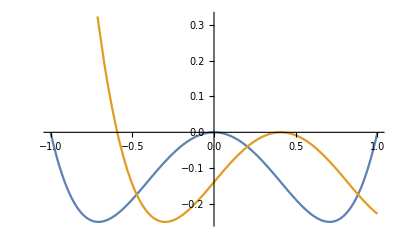

```mathematica
f[x_]:=x^4-x^2;
f2=inflectionShift[f,f''];
Plot[{f[x],f2[x]},{x,-1,1}]
```

```mathematica
vacuumShift[fun_]:=Module[{vac,fun2},
vac = Minimize[fun[x],x];
fun2[x_]=fun[x]-vac[[1]];
Return[fun2]]
```

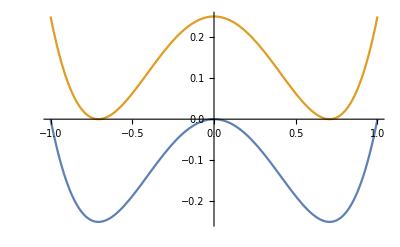

```mathematica
f[x_]:=x^4-x^2;
f2=vacuumShift[f];
Plot[{f[x],f2[x]},{x,-1,1},PlotRange->Full]
```

```mathematica
SolveVolterraEqn[g_,x0_,y_,xmax_]:=Module[{x1,y1,nn},
(* Solve y = ∫_x0^x1 g[x]ⅆx for x1 in the range x0 to xmax *)
(* Works for going either left or right (dending on if x0>or<xmax *)
nn = 1;
x1 = x0+(xmax-x0)/2^nn;
While[True,
y1 = NIntegrate[g[x],{x,x0,x1}];
If[Abs[y1-y]<eps,Break[]];
nn = nn+1;
If[y1>y,x1 = x1 -(xmax-x0)/2^nn;,
x1 = x1 +(xmax-x0)/2^nn;];
];
Return[x1]]
```

```mathematica
v[x_]:=(0.01)*((x^2-(10)^2)^2 );
g[x_]=v[x]/v'[x];
SolveVolterraEqn[g,8.6,80,0]
```

0.24226

```mathematica
v[x_]:=(0.1)*(1+Log[x]+0.001*x^4);
g[x_]=v[x]/v'[x];
SolveVolterraEqn[g,0.8,80,100]
```

20.9486

## Cosmology Calculation Modules

```mathematica
findZϵsr[v_,vp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ϵsr,f,z,num,ii,ztot},
ϵsr[x_]:=1/2*(vp[x]/v[x])^2;
f[n_]:=ϵsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZϵ[v_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{hsq,ϵ,f,z,num,ii,ztot},
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϵ[n_] = Evaluate[3*ϕ'[n]^2/(ϕ'[n]^2+2*v[ϕ[n]]/hsq[n])];
f[n_] = ϵ[n]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵ"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵ is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵ[ϕ[n]],{n,ii}]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZη[v_,vpp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ηsr,f,z,num,ii,ztot},
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]];
f[n_]:=ηsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ηsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ηsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ηsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of η is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findH[v_]:=Module[{h,hsq},
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
Return[{h,hsq}]]
```

### Find Initial Conditions for 1st Integration

```mathematica
chooseϕ0Manual[ϕ0list_]:=Module[{ϕ0index,ϕ0},
ϕ0index = Input["Enter the index for the ϕ0 you want to use: \n(Counting starts at 1)"];
ϕ0 = ϕ0list[[ϕ0index]]; 
Return[ϕ0]]
```

```mathematica
chooseϕ0Left[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#>0&];
(* vacuum = First[Select[ϕ0listpos,v[#]<10^-6&]];
ϕ0 = Max[Select[ϕ0listpos,#<vacuum&]]; *)
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0list],
ϕ0 = Min[Select[ϕ0list,#<First[vacuumArray]&]]];,
(*else*)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0listpos],
ϕ0 = Max[Select[ϕ0listpos,#<First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
chooseϕ0Right[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#≥0&];
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0list],
ϕ0 = Max[Select[ϕ0list,#>First[vacuumArray]&]]];,
(* else *)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0listpos],
ϕ0 = Min[Select[ϕ0listpos,#>First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
guessϕiLeft[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#<ϕ0&]];
Return[ϕiguess]]
```

```mathematica
guessϕiRight[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#>ϕ0&]];
Return[ϕiguess]]
```

```mathematica
findICsr[v_,vp_,vpp_,ni_,plots_,prints_,left_]:=Module[{ϕ0list,ϕ0index,ϕ0,f,ϕiguess,ϕi1s,ϕi1,ϕpi1,vplt,ϕ0plt,ϕiplt,ϕi1sol,ϕmax},
vplt = Plot[v[x],{x,-5,12},AxesLabel->{"ϕ","V"},PlotRange->Full];
(* Solve for where ϵ=1 and hence N=0 *)
ϕ0list = Normal[NSolve[vp[x]==√2*v[x],x,Reals]]/.C[1]->0;
ϕ0list = Values[stripList[Union[ϕ0list,Normal[NSolve[vp[x]==-√2*v[x],x,Reals]]/.C[1]->0]]];
Print["ϕ0list = ",ϕ0list];
If[plots,ϕ0plt = ListPlot[Transpose[{ϕ0list,v[ϕ0list]}]]; (* Transpose is Zip!! *)
Print[Show[vplt,ϕ0plt]]];
If[left,ϕ0 = chooseϕ0Left[ϕ0list,v],ϕ0 = chooseϕ0Right[ϕ0list,v]];
If[prints,Print["ϕ0 = ",ϕ0]];
If[ϕ0==∞,Abort[]];
If[ϕ0==-∞,Abort[]];
(* Integrate up the hill to find the value of ϕ at ni *)
Clear[x,t];
(* f[t_] := Integrate[v[x]/vp[x],{x,ϕ0,t}];
If[prints,Print["f[t] = ",f[t]]]; 
If[left,ϕi1s = t/.NSolve[ni==f[t]&&t≥0 && t≤ϕ0,t];,
ϕi1s = t/.NSolve[ni==f[t]&&t≥0 && t≥ϕ0,t]];
If[prints,Print["ϕi1s = NSolve[ni==f[t]] = ",ϕi1s]];
If[ϕi1s==t,Abort[]];
ϕi1 = Last[ϕi1s]; *)
g[x_]=v[x]/vp[x];
If[left,ϕmax=0,ϕmax=50];
ϕi1 = SolveVolterraEqn[g,ϕ0,ni,ϕmax];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
If[plots,ϕiplt = ListPlot[{{ϕi1,v[ϕi1]},{ϕ0,v[ϕ0]}}];
Print[Show[vplt,ϕiplt]]];
Return[{ϕi1,ϕpi1}]]
```

### Find Initial Conditions for 2nd Integration

```mathematica
findICshifted[v_,ϕsol1_,prints_,plots_]:=Module[{ϵ1,n1,ϕi2,ϕpi2},
(* Find ϵ1 *)
ϵ1=findϵ[v,ϕsol1];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ1[n]],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
If[n1==n1guess, Abort[]];
(* Find the new initial conditions *)
ϕi2 = Re[ϕ[ni2+n1]/.ϕsol1];
If[prints,Print["ϕi2 = ",ϕi2]];
ϕpi2 = Re[D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1)];
If[prints,Print["ϕpi2 = ",ϕpi2]];
Return[{ϕi2,ϕpi2}]]
```

```mathematica
solveKG[hsq_,vp_,ni_,nf_,ϕi1_,ϕpi1_,plots_]:=Module[{ϕsol1},
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,ni},AxesLabel->{N,"ϕsol"},GridLines->{{-1,-1.2},{1}}]]];
Return[ϕsol1]]
```

### Find Epsilon

```mathematica
findϵ[v_,ϕsol_]:=Module[{ϕp,hsq,ϵ,η},
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol;
ϵ[n_] = Evaluate[3*ϕp[n]^2/(ϕp[n]^2+2*v[ϕ[n]]/hsq[n])/.ϕsol];
(* above took out a Re[] just inside the Evaluate[] *)
(* η[n_] = D[ϵ[n],n]; *)
Return[ϵ]]
```

```mathematica
findϕsol[v_,vp_,vpp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_,left_]:=Module[{h,hsq,ϕi1,ϕpi1,ϕsol1,ϕi2,ϕpi2,ϕsol2},
(* Define the hubble parameter *)
{h,hsq}=findH[v];
(* Find the slow roll initial conditions *)
{ϕi1,ϕpi1}=findICsr[v,vp,vpp,ni,plots,prints,left];
(* Solve the Klein-Gordon equation for ϕ1[n] *)
ϕsol1 = solveKG[hsq,vp,ni,nf,ϕi1,ϕpi1,plots];
(* Find the new initial conditions and re-solve the KG equation *)
{ϕi2,ϕpi2}=findICshifted[v,ϕsol1,prints,plots];
ϕsol2 = solveKG[hsq,vp,ni2,nf2,ϕi2,ϕpi2,plots];
(* Note: before I had it integrating from nf2 to ni2 *)
If[prints,Print["ϕsol2[60] = ",ϕ[60]/.ϕsol2]];
Return[ϕsol2]]
```

```mathematica
findNsR[v_,vp_,ϕsol2_,ni2_,nf2_,plots_,prints_] := Module[{ϕ2p,h2sq,ϵ2,ns,r,ϵsr,ϵsrL,ηsr,ηsrL,Zϵ,Zη },
(* Find ϵ2 *)
ϵ2 = findϵ[v,ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ2[n]],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*ϵ2[n];
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,nf2,ni2},AxesLabel->{N,"ns"}]]];
Return[{ns[n],r[n],ϵ2}]];
```

```mathematica
findSRparams[v_,vp_,vpp_,ϕsol2_,ni2_,nf2_,prints_,plots_]:=Module[{ϵsr,ϵsrL,ηsr,ηsrL},
(* Find slow roll params ϵsr and ηsr *)
ϵsr[n_]:=1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol2;
ϵsrL[n_]:=1/2*D[Log[v[ϕ[n]]],n]/.ϕsol2;
If[prints,Print["ϵsr[0] = ",ϵsr[n]/.{n->0}]];
If[prints,Print["ϵsr[60] = ",ϵsr[n]/.{n->60}]];
If[prints,Print["ϵsrL[0] = ",ϵsrL[n]/.{n->0}]];
If[prints,Print["ϵsrL[60] = ",ϵsrL[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[1/2*(vp[x]/v[x])^2],{x,0,30},AxesLabel->{"ϕ","ϵ[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ϵsr[n]],"ϵsr"],Legended[ϵ2[n],"ϵ2"],Legended[Evaluate[ϵsrL[n]],"ϵsrL"]},{n,nf2,ni2},AxesLabel->{N,"ϵsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]]/.ϕsol2;
ηsrL[n_]:=1/2*D[Log[vp[ϕ[n]^2]],n]/.ϕsol2;If[prints,Print["ηsr[0] = ",ηsr[n]/.{n->0}]];
If[prints,Print["ηsr[60] = ",ηsr[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[vpp[x]/v[x]],{x,0,30},AxesLabel->{"ϕ","η[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
Return[{ϵsr,ηsr,ηsrL}]]
```

## Define Potential & Solve for Cosmological Parameters

#### (run the next two cells to get desired output!)

```mathematica
(* Define an inflationary potential *)
(* v[x_]:=x^(2/3); *) (* works *)
(* v[x_]:=(0.01)*((x^2-(10)^2)^2 ); *) (* works *)
(* v[x_]:=1/2*(1+Cos[0.5*x]); *)(* broke 8.8388*)
(* v[x_]:=0.5*(1+cosExpansion[0.5*x]); *)
(* v[x_]:=(0.5)*(1+Cos[x/4.0]); *) (* broke 8.8388 *)
(* v[x_]:=(0.01)*(1-(1/x)^2); *) (* D-brane *)
(* v[x_]:=(0.01)*(1-Exp[-0.01*x]); *) (* exponential *)
(*v[x_]:=(0.1)*(1-Exp[-(0.1)*x]);*) (* works *)
(*v[x_]:=(0.1)*(1+10*Exp[-2*x/√6])^-2;*) (* works *) 
(* v[x_]:=(0.1)*(1+Exp[-2*x/√6])^-2; *) (* works *) (* Shaposhnikov model *)
(* v[x_]:=(0.1)*(1-Exp[-√(2/3)*x])^2; *) (* Starobinsky model *)
(* v[x_]:=1-2/(5)^2*x^2;  *)
(* v[x_]:=x^4; *) (* works *)
(* v[x_] := 1-1/2*(0.7)^2*x^2+(44^2/0.7)*x^4; *)
(* Plot[v[x],{x,-10,10}] *)
(* "{a,b,c,g} = "-1/50", "0.0001", "1/10000", "1.1058412850778434 *)
(* a = -1/50;
b = -0.0001;
c = 1/10000;
g = 1.105841285077843;
d = 0.01*10^4;
v[x_]:=d*(g + a*x^2 + b*x^3 + c*x^4);
v = inflectionShift[v,v''];
v = vacuumShift[v];*)
left = True;
(*v[x_]:=(1-2*(2/8^2)*x^2+(1/8^4)*x^4);*)
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -2.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -2;
```

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

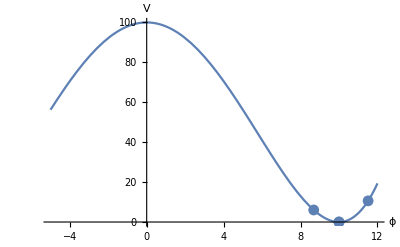

vacuumArray = {10.,10.}

ϕ0 = 8.68529

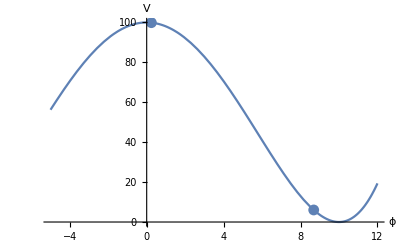

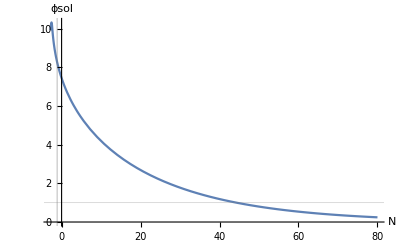

At n = 0, ϵ1 = 0.186962

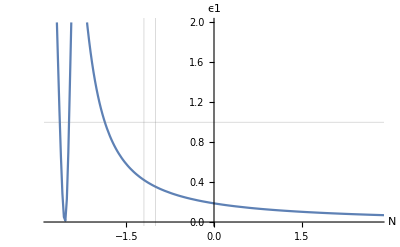

At n1 = -1.86953, ϵ1 = 1.

ϕi2 = 0.261526

ϕpi2 = -0.0103324

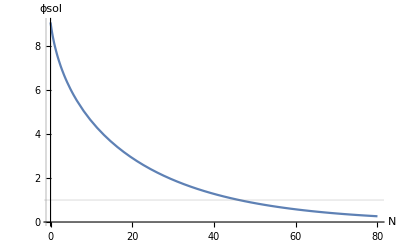

ϕsol2[60] = 0.576753

At n = 0, ϵ1 = 1.00001

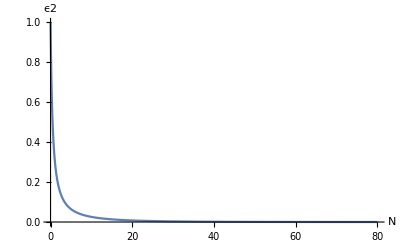

ns[60] = 0.919755

r[60] = 0.00417463

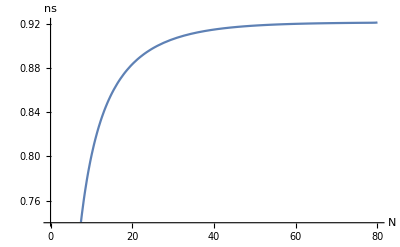

ϵsr[0] = 2.12062

ϵsr[60] = 0.000267895

ϵsrL[0] = 1.45624

ϵsrL[60] = 0.000264381

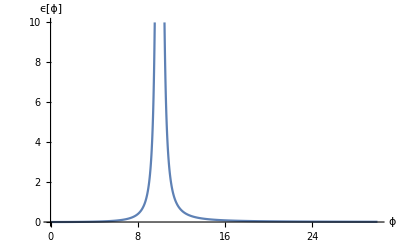

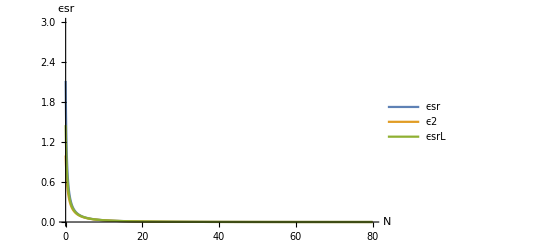

ηsr[0] = 1.89371

ηsr[60] = -0.0398656

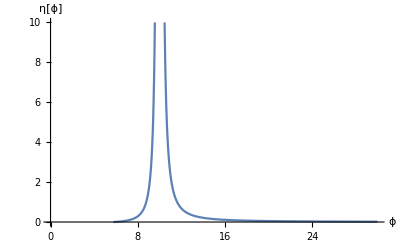

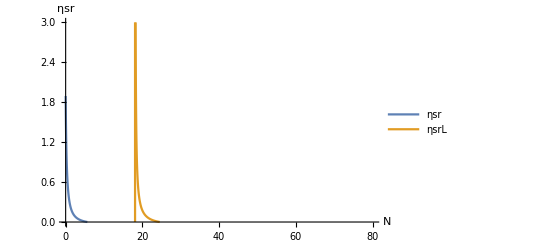

```mathematica
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True];
findSRparams[v,vp,vpp,ϕsol2,ni2,nf2,True,True]];
```

## Replicate Planck Plot

### Plotting Module

```mathematica
plotPotential[va_,left_,aList_,mark_,col_]:=Module[{p1,p2},
ns60List={};ns50List={};r60List={};r50List={};
Do[
v[x_]:=va[x,a];
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{a,aList}]
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p1 = ListPlot[Legended[Transpose[{ns60Listq,r60Listq}],"Exponential at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,20},PlotStyle->col];
p2 = ListPlot[Legended[Transpose[{ns50Listq,r50Listq}],"Exponential at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,12},PlotStyle->col];
Return[{p1,p2}]];
```

```mathematica
v[x_,a_]:=(0.01)*(1-Exp[-a*x]);
aList = {0.01,0.05,0.1,0.5,1};
{p14, p15} = plotPotential[v,False,aList,●,Purple];
Show[p14,p15]
```

#### Hilltop Models: V=λ(ϕ^2 - σ^2)^2

```mathematica
σList = {5,7,10,12,15,17,20,22,25,26,30,40,50,60,70,80,100};
ns60List={};ns50List={};r60List={};r50List={};
Do[
Print["σ = ",σ];
v[x_]:=(0.01)*((x^2-(σ)^2)^2 );
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{σ,σList}]
```

```mathematica
ns60List
r60List
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[Legended[Transpose[{ns60List,r60List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Green];
p2 = ListPlot[Legended[Transpose[{ns50List,r50List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Green,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

Show[p1,p2]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

```mathematica
μList = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ={};ns50Listμ={};r60Listμ={};r50Listμ={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^2);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ,ns/.{n->60}];
AppendTo[ns50Listμ,ns/.{n->50}];
AppendTo[r60Listμ,r/.{n->60}];
AppendTo[r50Listμ,r/.{n->50}];
,{μ,μList}]
```

```mathematica
ns60Listμ
r60Listμ
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p3 = ListPlot[Legended[Transpose[{ns60Listμ,r60Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Blue];
p4 = ListPlot[Legended[Transpose[{ns50Listμ,r50Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Blue,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p1,p2,p3,p4]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

```mathematica
μ4List = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ4={};ns50Listμ4={};r60Listμ4={};r50Listμ4={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^4);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ4,ns/.{n->60}];
AppendTo[ns50Listμ4,ns/.{n->50}];
AppendTo[r60Listμ4,r/.{n->60}];
AppendTo[r50Listμ4,r/.{n->50}];
,{μ,μ4List}]
```

```mathematica
ns60Listμ4
r60Listμ4
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p5 = ListPlot[Legended[Transpose[{ns60Listμ4,r60Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Cyan];
p6 = ListPlot[Legended[Transpose[{ns50Listμ4,r50Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Cyan,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p5,p6]
```

### Natural Inflation Models: V=λ(1 + Cos(ϕ/ff) )

```mathematica
fList = {3};(*{5,7,10,12,15,17,20,22,25};*)
ns60Listf={};ns50Listf={};r60Listf={};r50Listf={};
Do[
v[x_]:= 0.5*(0.01)*(1+Cos[x/ff]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True]; 
AppendTo[ns60Listf,ns/.{n->60}];
AppendTo[ns50Listf,ns/.{n->50}];
AppendTo[r60Listf,r/.{n->60}];
AppendTo[r50Listf,r/.{n->50}];
,{ff,fList}]
```

```mathematica
ns50Listf
r50Listf
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p5 = ListPlot[Transpose[{ns60Listf,r60Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=60"}]];
p6 = ListPlot[Transpose[{ns50Listf,r50Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p5,p6]
```

### Starobinsky’s R^2 Model: V(ϕ)=M_pl^2/(4α)(1-exp[-√(2/3)ϕ/M_pl])^2

```mathematica
v[x_]:=(0.1)*(1-Exp[-√(2/3)*x])^2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p7 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Starobinsky at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Purple];
p8 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Starobinsky at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p7,p8]
```

### Shaposhnikov model: V(ϕ)=λM_pl^2/(4 ξ^2)(1+exp[(-2ϕ)/(√6 M_pl)])^-2

```mathematica
v[x_]:=(0.1)*(1+Exp[-2*x/√6])^-2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p9 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Shaposhinikov at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Blue];
p10 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Shaposhnikov at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Blue];
Show[p7,p8,p9,p10]
```

### D-brane inflation: V(ϕ)=λ^4(1-(m/ϕ)^p)

```mathematica
mList = {1,10,20,40,60,80,100};
pList={1,2,3,4};
colorList = {Red,Green,Blue,Orange}; jj=1;
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2; p11={};p12={};
Do[ns60Listm={};ns50Listm={};r60Listm={};r50Listm={};
Do[
Print["m = ",m];
Print["jj = ",jj];
v[x_]:=(0.01)*(1-(m/x)^p);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listm,ns/.{n->60}];
AppendTo[ns50Listm,ns/.{n->50}];
AppendTo[r60Listm,r/.{n->60}];
AppendTo[r50Listm,r/.{n->50}];
,{m,mList}]
AppendTo[p11, ListPlot[Legended[Transpose[{ns60Listm,r60Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,20},PlotStyle->colorList[[jj]]]];
AppendTo[p11 , ListPlot[Legended[Transpose[{ns50Listm,r50Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,12},PlotStyle->colorList[[jj]]]];
jj = jj+1;
,{p,pList}];

Show[p11]
```

### Exponential potential: V(ϕ)=λ^4(1-exp[-qϕ/M_pl])

```mathematica
qList = {0.01,0.05,0.1,0.5,1};
ns60Listq={};ns50Listq={};r60Listq={};r50Listq={};
Do[
v[x_]:=(0.01)*(1-Exp[-q*x]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listq,ns/.{n->60}];
AppendTo[ns50Listq,ns/.{n->50}];
AppendTo[r60Listq,r/.{n->60}];
AppendTo[r50Listq,r/.{n->50}];
,{q,qList}]
```

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p12 = ListPlot[Legended[Transpose[{ns60Listq,r60Listq}],"Exponential at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple];
p13 = ListPlot[Legended[Transpose[{ns50Listq,r50Listq}],"Exponential at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p12,p13]
```

### Spontaneously Broken SUSY: V(ϕ)=λ^4(1+a*log[ϕ/M_pl])

## Monomial Loop for Planck Plot

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 60; nf = -1.8; ni2 = 60; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35;
Do[
Clear[v,vp,vpp,ns,r,ϵ2];
v[x_] := x^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```

## Find Zeros

### Loop over polynomial perturbations of the hilltop model

{0.,{x→10.}}

{a,b,c,g} = -1/50, 0, 1/10000, 1.

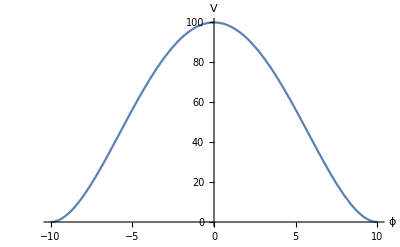

PASSED

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

vacuumArray = {10.,10.}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕi1s = {0.242866}

InterpolatingFunction::dmval: Input value {-3.23078} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.60497} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.31669} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::reged: The point {80.} is at the edge of the search region {0., 80.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: reged will be suppressed during this calculation.

{80.}

{a,b,c,Z} = -1/50, 0, 1/10000, 0

{9.09091,{x→-9.53463}}

{a,b,c,g} = -1/50, 0, 0.00011, 0.909091

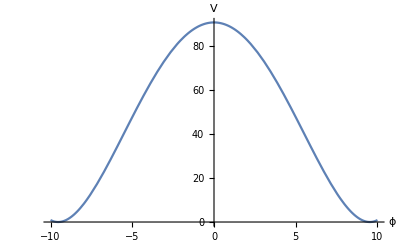

PASSED

ϕ0list = {-11.0531,-9.53463,-9.53463,-8.22472,8.22472,9.53463,9.53463,11.0531}

vacuumArray = {9.53463,9.53463}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕi1s = {0.167838}

{80.}

{a,b,c,Z} = -1/50, 0, 0.00011, 0

{16.6667,{x→9.12871}}

{a,b,c,g} = -1/50, 0, 0.00012, 0.833333

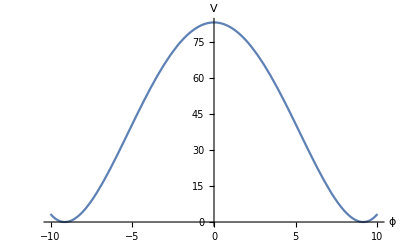

PASSED

ϕ0list = {-10.6518,-9.12871,-9.12871,-7.82339,7.82339,9.12871,9.12871,10.6518}

vacuumArray = {9.12871,9.12871}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve :: ratnz will be suppressed during this calculation.

ϕi1s = {0.11648}

{80.}

{a,b,c,Z} = -1/50, 0, 0.00012, 0

{-11.1111,{x→10.5409}}

{a,b,c,g} = -1/50, 0, 0.00009, 1.11111

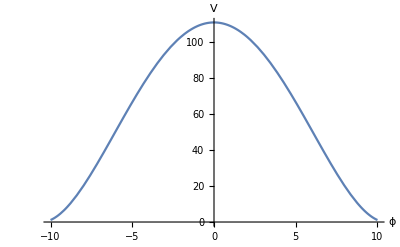

PASSED

ϕ0list = {-12.0496,-10.5409,-9.22116,9.22116,10.5409,12.0496}

vacuumArray = {10.5409}

ϕi1s = {0.353253}

{80.}

{a,b,c,Z} = -1/50, 0, 0.00009, 0

{-25.,{x→11.1803}}

{a,b,c,g} = -1/50, 0, 0.00008, 1.25

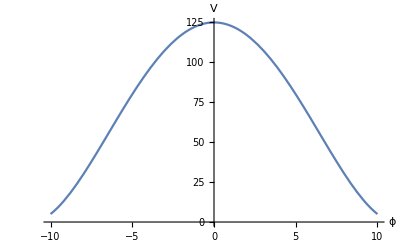

PASSED

ϕ0list = {-12.6836,-11.1803,-11.1803,-9.85521,9.85521,11.1803,11.1803,12.6836}

vacuumArray = {11.1803,11.1803}

ϕi1s = {0.517146}

{80.}

{a,b,c,Z} = -1/50, 0, 0.00008, 0

{23.0769,{x→8.77058}}

{a,b,c,g} = -1/50, 0, 0.00013, 0.769231

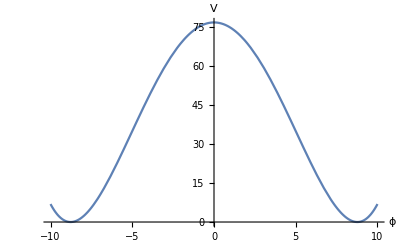

PASSED

ϕ0list = {-10.2981,-8.77058,-8.77058,-7.46965,7.46965,8.77058,8.77058,10.2981}

vacuumArray = {8.77058,8.77058}

ϕi1s = {0.0811236}

{80.}

{a,b,c,Z} = -1/50, 0, 0.00013, 0

{-42.8571,{x→11.9523}}

{a,b,c,g} = -1/50, 0, 0.00007, 1.42857

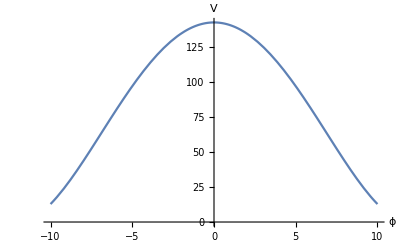

PASSED

ϕ0list = {-13.4499,-11.9523,-11.9523,-10.6214,10.6214,11.9523,11.9523,13.4499}

vacuumArray = {11.9523,11.9523}

ϕi1s = {0.763427}

{80.}

{a,b,c,Z} = -1/50, 0, 0.00007, 0

{-10.5841,{x→-10.382}}

{a,b,c,g} = -1/50, 0.0001, 1/10000, 1.10584

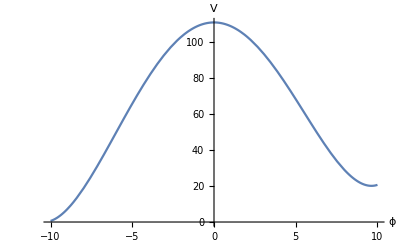

PASSED

ϕ0list = {-11.8934,-10.382,-10.382,-9.0648}

vacuumArray = {-10.382,-10.382}

ϕi1s = t

ABORTED

{-0.0588317,{x→-9.88163}}

{a,b,c,g} = -1/50, 0.0001, 0.00011, 1.00059

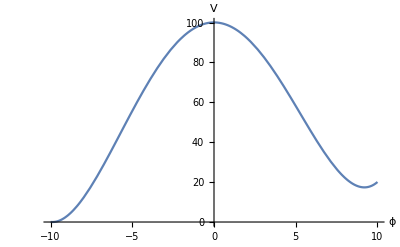

PASSED

ϕ0list = {-11.3978,-9.88163,-9.88163,-8.5692}

vacuumArray = {-9.88163,-9.88163}

ϕi1s = t

ABORTED

{8.6551,{x→-9.44656}}

{a,b,c,g} = -1/50, 0.0001, 0.00012, 0.913449

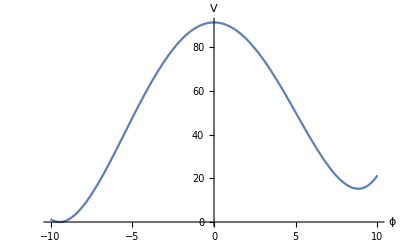

PASSED

ϕ0list = {-10.9673,-9.44656,-9.44656,-8.13871}

vacuumArray = {-9.44656,-9.44656}

ϕi1s = t

ABORTED

{-23.5459,{x→-10.9658}}

{a,b,c,g} = -1/50, 0.0001, 0.00009, 1.23546

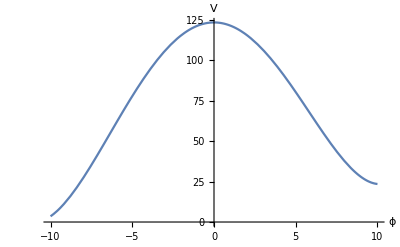

PASSED

ϕ0list = {-12.4721,-10.9658,-10.9658,-9.64354}

vacuumArray = {-10.9658,-10.9658}

ϕi1s = t

ABORTED

{-39.8922,{x→-11.6589}}

{a,b,c,g} = -1/50, 0.0001, 0.00008, 1.39892

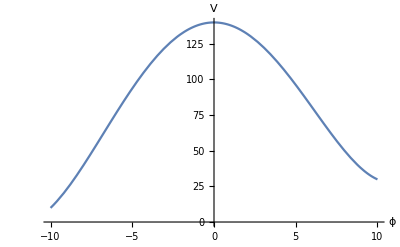

PASSED

ϕ0list = {-13.1598,-11.6589,-11.6589,-10.3313}

vacuumArray = {-11.6589,-11.6589}

ϕi1s = t

ABORTED

{15.9863,{x→-9.06378}}

{a,b,c,g} = -1/50, 0.0001, 0.00013, 0.840137

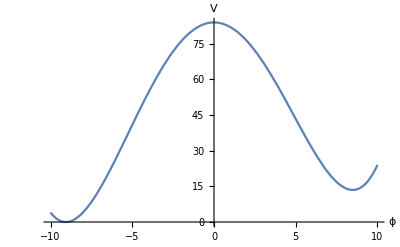

PASSED

ϕ0list = {-10.5889,-9.06378,-9.06378,-7.76033}

vacuumArray = {-9.06378,-9.06378}

ϕi1s = t

ABORTED

{-26.8805,{x→11.4286}}

{a,b,c,g} = -1/50, 0.0001, 0.00007, 1.2688

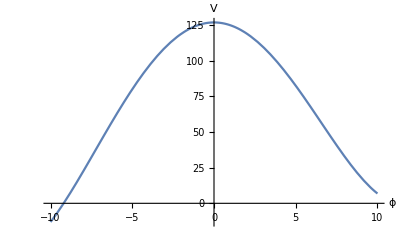

PASSED

ϕ0list = {-15.9265,-14.4928,-9.85937,-8.46452,10.1003,11.4286,12.9286}

vacuumArray = {11.4286}

ϕi1s = {0.567543}

{80.}

{a,b,c,Z} = -1/50, 0.0001, 0.00007, 0

{-10.5841,{x→10.382}}

{a,b,c,g} = -1/50, -0.0001, 1/10000, 1.10584

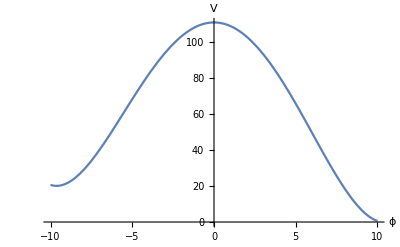

PASSED

ϕ0list = {9.0648,10.382,11.8934}

vacuumArray = {10.382}

ϕi1s = {0.332946}

{80.}

{a,b,c,Z} = -1/50, -0.0001, 1/10000, 0

{-0.0588317,{x→9.88163}}

{a,b,c,g} = -1/50, -0.0001, 0.00011, 1.00059

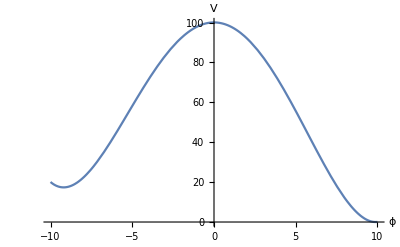

PASSED

ϕ0list = {8.5692,9.88163,9.88163,11.3978}

vacuumArray = {9.88163,9.88163}

ϕi1s = {0.233494}

{80.}

{a,b,c,Z} = -1/50, -0.0001, 0.00011, 0

{8.6551,{x→9.44656}}

{a,b,c,g} = -1/50, -0.0001, 0.00012, 0.913449

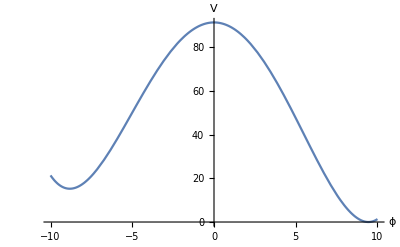

PASSED

ϕ0list = {8.13871,9.44656,9.44656,10.9673}

vacuumArray = {9.44656,9.44656}

ϕi1s = {0.164372}

{80.}

{a,b,c,Z} = -1/50, -0.0001, 0.00012, 0

{-23.5459,{x→10.9658}}

{a,b,c,g} = -1/50, -0.0001, 0.00009, 1.23546

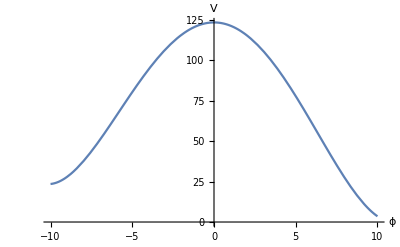

PASSED

ϕ0list = {9.64354,10.9658,10.9658,12.4721}

vacuumArray = {10.9658,10.9658}

ϕi1s = {0.477023}

{80.}

{a,b,c,Z} = -1/50, -0.0001, 0.00009, 0

{-39.8922,{x→11.6589}}

{a,b,c,g} = -1/50, -0.0001, 0.00008, 1.39892

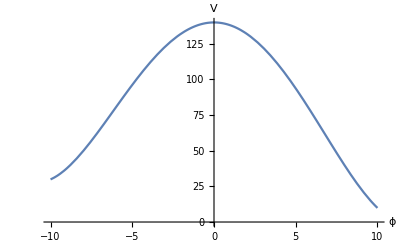

PASSED

ϕ0list = {10.3313,11.6589,11.6589,13.1598}

vacuumArray = {11.6589,11.6589}

ϕi1s = {0.687639}

{80.}

{a,b,c,Z} = -1/50, -0.0001, 0.00008, 0

{15.9863,{x→9.06378}}

{a,b,c,g} = -1/50, -0.0001, 0.00013, 0.840137

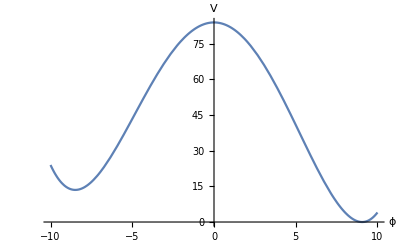

PASSED

ϕ0list = {7.76033,9.06378,9.06378,10.5889}

vacuumArray = {9.06378,9.06378}

ϕi1s = {0.116073}

{80.}

{a,b,c,Z} = -1/50, -0.0001, 0.00013, 0

{-61.1328,{x→12.5}}

{a,b,c,g} = -1/50, -0.0001, 0.00007, 1.61133

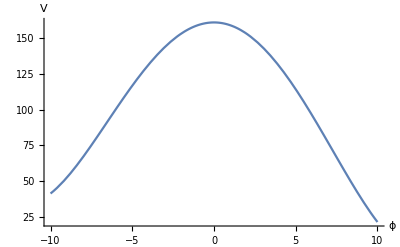

PASSED

ϕ0list = {11.1666,12.5,13.9952}

vacuumArray = {12.5}

ϕi1s = {0.999315}

{80.}

{a,b,c,Z} = -1/50, -0.0001, 0.00007, 0

{-183.342,{x→-14.43}}

{a,b,c,g} = -1/50, 0.001, 1/10000, 2.83342

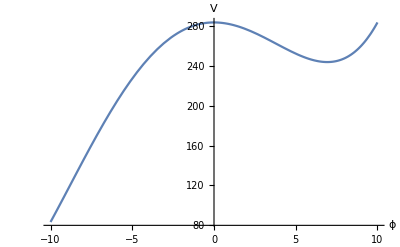

PASSED

ϕ0list = {-15.9217,-14.43,-14.43,-13.0926}

vacuumArray = {-14.43,-14.43}

ϕi1s = t

ABORTED

{-145.179,{x→-13.5348}}

{a,b,c,g} = -1/50, 0.001, 0.00011, 2.45179

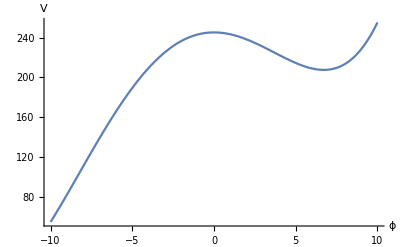

PASSED

ϕ0list = {-15.0313,-13.5348,-13.5348,-12.2022}

vacuumArray = {-13.5348,-13.5348}

ϕi1s = t

ABORTED

{-115.277,{x→-12.7738}}

{a,b,c,g} = -1/50, 0.001, 0.00012, 2.15277

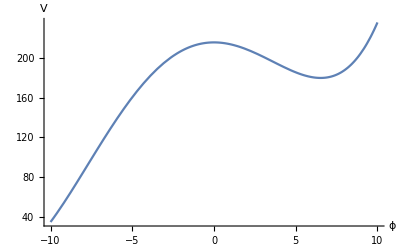

PASSED

ϕ0list = {-14.2748,-12.7738,-12.7738,-11.4456}

vacuumArray = {-12.7738,-12.7738}

ϕi1s = t

ABORTED

{-233.407,{x→-15.5012}}

{a,b,c,g} = -1/50, 0.001, 0.00009, 3.33407

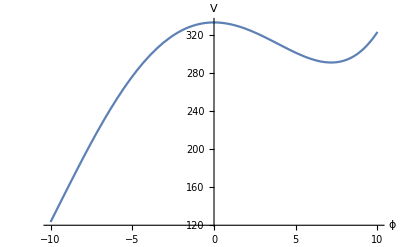

PASSED

ϕ0list = {-16.988,-15.5012,-15.5012,-14.1589}

vacuumArray = {-15.5012,-15.5012}

ϕi1s = t

ABORTED

{-301.369,{x→-16.8107}}

{a,b,c,g} = -1/50, 0.001, 0.00008, 4.01369

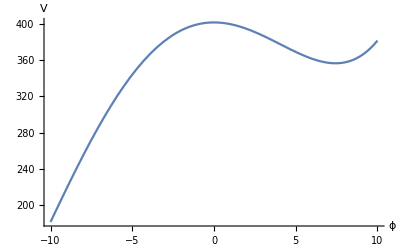

PASSED

ϕ0list = {-18.2922,-16.8107,-16.8107,-15.4632}

vacuumArray = {-16.8107,-16.8107}

ϕi1s = t

ABORTED

{-91.3113,{x→-12.1174}}

{a,b,c,g} = -1/50, 0.001, 0.00013, 1.91311

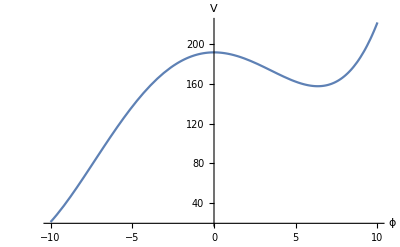

PASSED

ϕ0list = {-13.6228,-12.1174,-12.1174,-10.7935}

vacuumArray = {-12.1174,-12.1174}

ϕi1s = t

ABORTED

{-397.731,{x→-18.4551}}

{a,b,c,g} = -1/50, 0.001, 0.00007, 4.97731

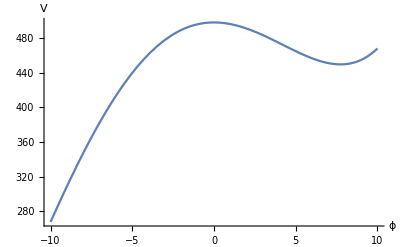

PASSED

ϕ0list = {-19.931,-18.4551,-18.4551,-17.1021}

vacuumArray = {-18.4551,-18.4551}

ϕi1s = t

ABORTED

{-183.342,{x→14.43}}

{a,b,c,g} = -1/50, -0.001, 1/10000, 2.83342

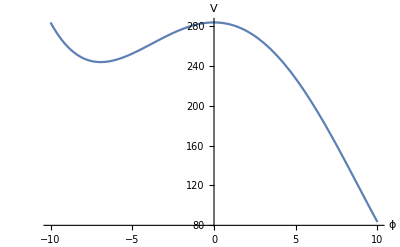

PASSED

ϕ0list = {13.0926,14.43,15.9217}

vacuumArray = {14.43}

ϕi1s = {2.20051}

{80.}

{a,b,c,Z} = -1/50, -0.001, 1/10000, 0

{-145.179,{x→13.5348}}

{a,b,c,g} = -1/50, -0.001, 0.00011, 2.45179

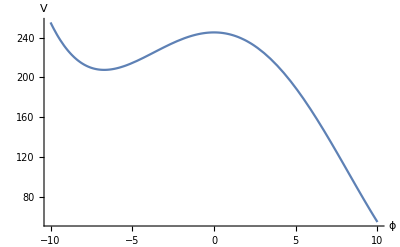

PASSED

ϕ0list = {12.2022,13.5348,13.5348,15.0313}

vacuumArray = {13.5348,13.5348}

ϕi1s = {1.7134}

{80.}

{a,b,c,Z} = -1/50, -0.001, 0.00011, 0

{-115.277,{x→12.7738}}

{a,b,c,g} = -1/50, -0.001, 0.00012, 2.15277

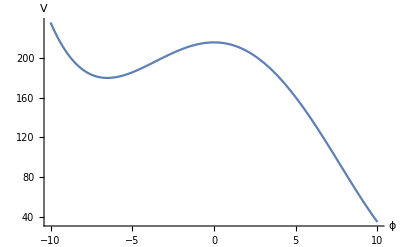

PASSED

ϕ0list = {11.4456,12.7738,14.2748}

vacuumArray = {12.7738}

ϕi1s = {1.3395}

{80.}

{a,b,c,Z} = -1/50, -0.001, 0.00012, 0

{-233.407,{x→15.5012}}

{a,b,c,g} = -1/50, -0.001, 0.00009, 3.33407

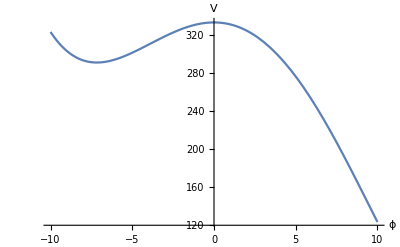

PASSED

ϕ0list = {14.1589,15.5012,15.5012,16.988}

vacuumArray = {15.5012,15.5012}

ϕi1s = {2.842}

{80.}

{a,b,c,Z} = -1/50, -0.001, 0.00009, 0

{-301.369,{x→16.8107}}

{a,b,c,g} = -1/50, -0.001, 0.00008, 4.01369

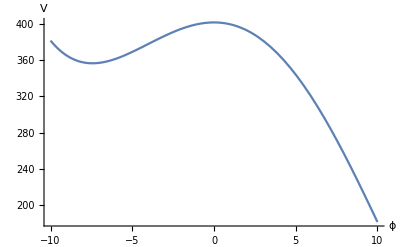

PASSED

ϕ0list = {15.4632,16.8107,16.8107,18.2922}

vacuumArray = {16.8107,16.8107}

ϕi1s = {3.69927}

{80.}

{a,b,c,Z} = -1/50, -0.001, 0.00008, 0

{-91.3113,{x→12.1174}}

{a,b,c,g} = -1/50, -0.001, 0.00013, 1.91311

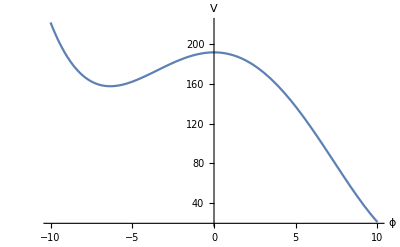

PASSED

ϕ0list = {10.7935,12.1174,12.1174,13.6228}

vacuumArray = {12.1174,12.1174}

ϕi1s = {1.05017}

{80.}

{a,b,c,Z} = -1/50, -0.001, 0.00013, 0

{-397.731,{x→18.4551}}

{a,b,c,g} = -1/50, -0.001, 0.00007, 4.97731

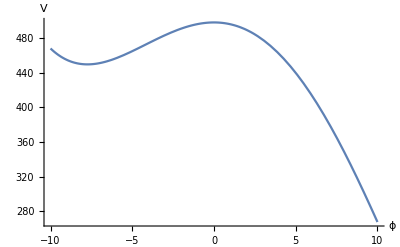

PASSED

ϕ0list = {17.1021,18.4551,18.4551,19.931}

vacuumArray = {18.4551,18.4551}

ϕi1s = {4.8679}

{80.}

{a,b,c,Z} = -1/50, -0.001, 0.00007, 0

{-67.0518,{x→-12.0493}}

{a,b,c,g} = -1/50, 0.0005, 1/10000, 1.67052

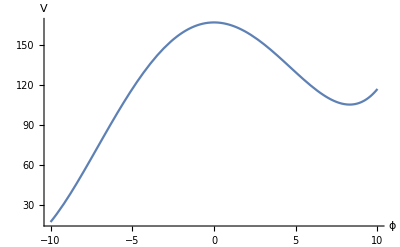

PASSED

ϕ0list = {-13.5515,-12.0493,-12.0493,-10.7225}

vacuumArray = {-12.0493,-12.0493}

ϕi1s = t

ABORTED

{-48.212,{x→-11.3903}}

{a,b,c,g} = -1/50, 0.0005, 0.00011, 1.48212

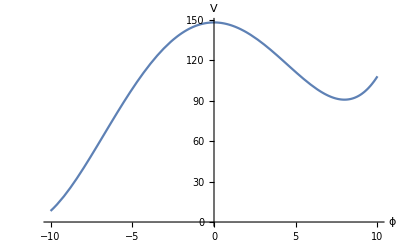

PASSED

ϕ0list = {-12.8974,-11.3903,-11.3903,-10.0684}

vacuumArray = {-11.3903,-11.3903}

ϕi1s = t

ABORTED

{-33.0097,{x→-10.824}}

{a,b,c,g} = -1/50, 0.0005, 0.00012, 1.3301

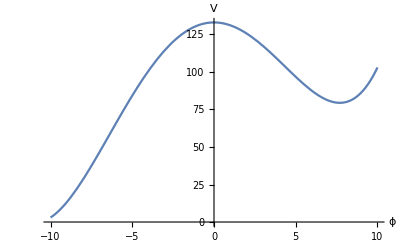

PASSED

ϕ0list = {-12.3356,-10.824,-10.824,-9.50656}

vacuumArray = {-10.824,-10.824}

ϕi1s = t

ABORTED

{-90.9496,{x→-12.8282}}

{a,b,c,g} = -1/50, 0.0005, 0.00009, 1.9095

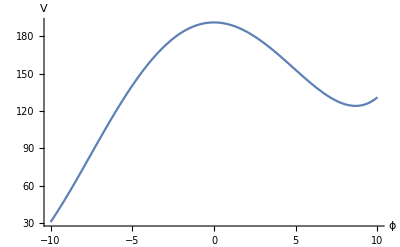

PASSED

ϕ0list = {-14.3253,-12.8282,-12.8282,-11.4964}

vacuumArray = {-12.8282,-12.8282}

ϕi1s = t

ABORTED

{-122.15,{x→-13.7671}}

{a,b,c,g} = -1/50, 0.0005, 0.00008, 2.2215

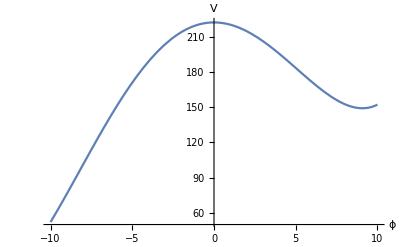

PASSED

ϕ0list = {-15.2589,-13.7671,-13.7671,-12.43}

vacuumArray = {-13.7671,-13.7671}

ϕi1s = t

ABORTED

{-20.5047,{x→-10.3307}}

{a,b,c,g} = -1/50, 0.0005, 0.00013, 1.20505

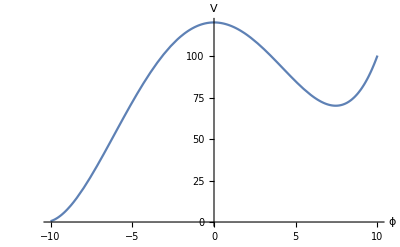

PASSED

ϕ0list = {-11.8467,-10.3307,-10.3307,-9.01765}

vacuumArray = {-10.3307,-10.3307}

ϕi1s = t

ABORTED

{-164.402,{x→-14.9273}}

{a,b,c,g} = -1/50, 0.0005, 0.00007, 2.64402

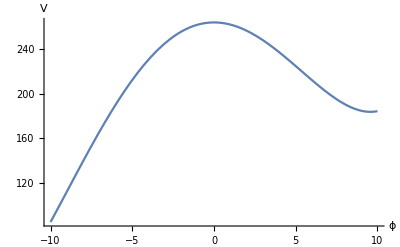

PASSED

ϕ0list = {-16.4134,-14.9273,-14.9273,-13.5846}

vacuumArray = {-14.9273,-14.9273}

ϕi1s = t

ABORTED

{-67.0518,{x→12.0493}}

{a,b,c,g} = -1/50, -0.0005, 1/10000, 1.67052

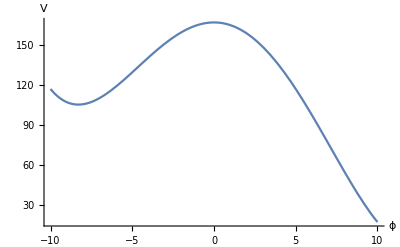

PASSED

ϕ0list = {10.7225,12.0493,12.0493,13.5515}

vacuumArray = {12.0493,12.0493}

ϕi1s = {0.921452}

{80.}

{a,b,c,Z} = -1/50, -0.0005, 1/10000, 0

{-48.212,{x→11.3903}}

{a,b,c,g} = -1/50, -0.0005, 0.00011, 1.48212

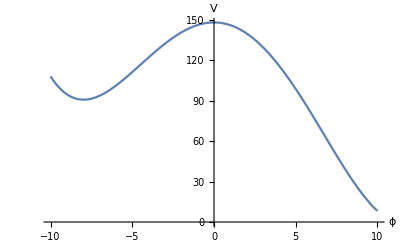

PASSED

ϕ0list = {10.0684,11.3903,11.3903,12.8974}

vacuumArray = {11.3903,11.3903}

ϕi1s = {0.681997}

{80.}

{a,b,c,Z} = -1/50, -0.0005, 0.00011, 0

{-33.0097,{x→10.824}}

{a,b,c,g} = -1/50, -0.0005, 0.00012, 1.3301

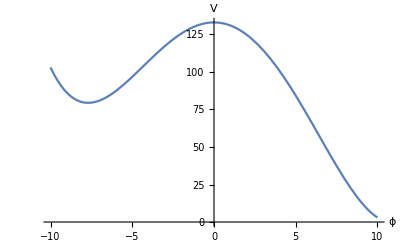

PASSED

ϕ0list = {9.50656,10.824,10.824,12.3356}

vacuumArray = {10.824,10.824}

ϕi1s = {0.506333}

{80.}

{a,b,c,Z} = -1/50, -0.0005, 0.00012, 0

{-90.9496,{x→12.8282}}

{a,b,c,g} = -1/50, -0.0005, 0.00009, 1.9095

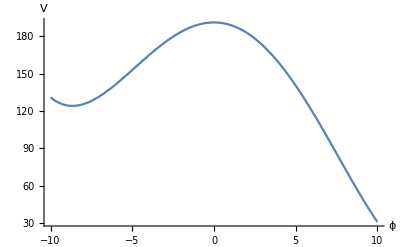

PASSED

ϕ0list = {11.4964,12.8282,12.8282,14.3253}

vacuumArray = {12.8282,12.8282}

ϕi1s = {1.25038}

{80.}

{a,b,c,Z} = -1/50, -0.0005, 0.00009, 0

{-122.15,{x→13.7671}}

{a,b,c,g} = -1/50, -0.0005, 0.00008, 2.2215

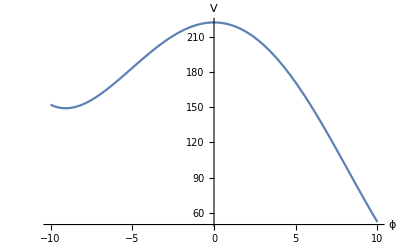

PASSED

ϕ0list = {12.43,13.7671,13.7671,15.2589}

vacuumArray = {13.7671,13.7671}

ϕi1s = {1.70711}

{80.}

{a,b,c,Z} = -1/50, -0.0005, 0.00008, 0

{-20.5047,{x→10.3307}}

{a,b,c,g} = -1/50, -0.0005, 0.00013, 1.20505

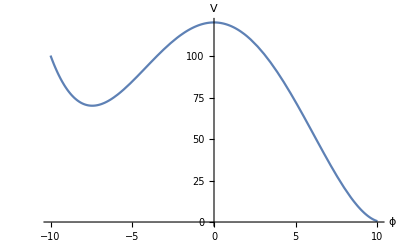

PASSED

ϕ0list = {9.01765,10.3307,10.3307,11.8467}

vacuumArray = {10.3307,10.3307}

ϕi1s = {0.376751}

{80.}

{a,b,c,Z} = -1/50, -0.0005, 0.00013, 0

{-164.402,{x→14.9273}}

{a,b,c,g} = -1/50, -0.0005, 0.00007, 2.64402

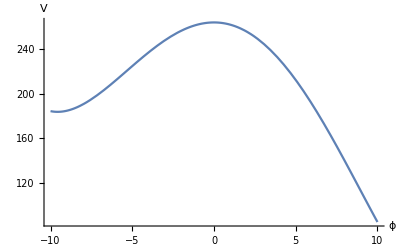

PASSED

ϕ0list = {13.5846,14.9273,14.9273,16.4134}

vacuumArray = {14.9273,14.9273}

ϕi1s = {2.35099}

{80.}

{a,b,c,Z} = -1/50, -0.0005, 0.00007, 0

{100.,{x→4.02341×10^-21}}

{100.,{x→4.5528×10^-21}}

{100.,{x→4.87044×10^-21}}

{100.,{x→3.70577×10^-21}}

{100.,{x→3.28225×10^-21}}

{100.,{x→5.29396×10^-21}}

{100.,{x→2.85874×10^-21}}

{100.,{x→2.61598×10^-15}}

{100.,{x→2.61598×10^-15}}

{100.,{x→2.61598×10^-15}}

«4 more identical outputs»

{100.,{x→-2.61597×10^-15}}

{100.,{x→-2.61597×10^-15}}

{100.,{x→-2.61597×10^-15}}

«4 more identical outputs»

{100.,{x→5.6798×10^-29}}

{100.,{x→5.36425×10^-29}}

{100.,{x→5.6798×10^-29}}

{100.,{x→5.6798×10^-29}}

{100.,{x→5.6798×10^-29}}

{100.,{x→5.36425×10^-29}}

{100.,{x→5.6798×10^-29}}

{100.,{x→-5.6798×10^-29}}

{100.,{x→-5.36425×10^-29}}

{100.,{x→-5.6798×10^-29}}

{100.,{x→-5.36425×10^-29}}

{100.,{x→-5.36425×10^-29}}

{100.,{x→-5.36425×10^-29}}

«1 more identical outputs»

{100.,{x→6.31089×10^-30}}

{100.,{x→6.31089×10^-30}}

{100.,{x→6.31089×10^-30}}

«1 more identical outputs»

{100.,{x→7.88861×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→-6.31089×10^-30}}

{100.,{x→-6.31089×10^-30}}

{100.,{x→-6.31089×10^-30}}

{100.,{x→-4.73317×10^-30}}

{100.,{x→-7.88861×10^-30}}

{100.,{x→-6.31089×10^-30}}

{100.,{x→-6.31089×10^-30}}

{-21.,{x→10.4881}}

{a,b,c,g} = -0.022, 0, 1/10000, 1.21

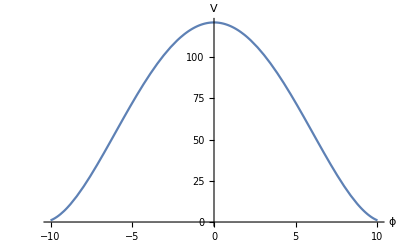

PASSED

ϕ0list = {-11.9972,-10.4881,-10.4881,-9.16879,9.16879,10.4881,10.4881,11.9972}

vacuumArray = {10.4881,10.4881}

ϕi1s = {0.34134}

{80.}

{a,b,c,Z} = -0.022, 0, 1/10000, 0

{-10.,{x→10.}}

{a,b,c,g} = -0.022, 0, 0.00011, 1.1

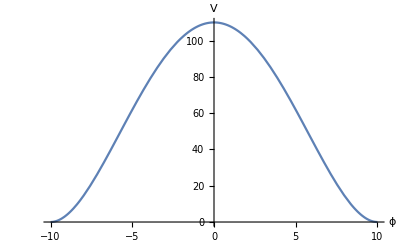

PASSED

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

vacuumArray = {10.,10.}

ϕi1s = {0.242866}

{80.}

{a,b,c,Z} = -0.022, 0, 0.00011, 0

{-0.833333,{x→-9.57427}}

{a,b,c,g} = -0.022, 0, 0.00012, 1.00833

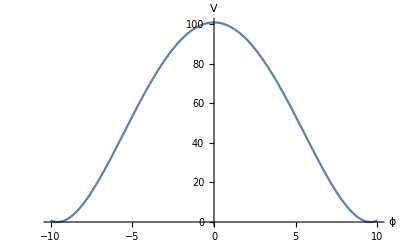

PASSED

ϕ0list = {-11.0924,-9.57427,-8.26394,8.26394,9.57427,11.0924}

vacuumArray = {9.57427}

ϕi1s = {0.17354}

{80.}

{a,b,c,Z} = -0.022, 0, 0.00012, 0

{-34.4444,{x→11.0554}}

{a,b,c,g} = -0.022, 0, 0.00009, 1.34444

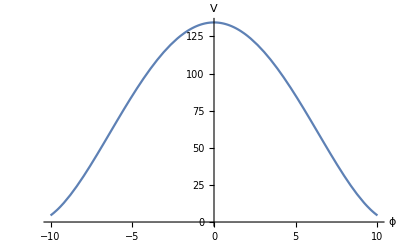

PASSED

ϕ0list = {-12.5597,-11.0554,-9.73129,9.73129,11.0554,12.5597}

vacuumArray = {11.0554}

ϕi1s = {0.482254}

{80.}

{a,b,c,Z} = -0.022, 0, 0.00009, 0

{-51.25,{x→11.726}}

{a,b,c,g} = -0.022, 0, 0.00008, 1.5125

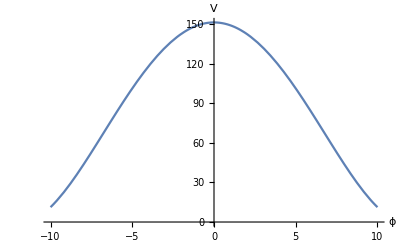

PASSED

ϕ0list = {-13.2252,-11.726,-11.726,-10.3968,10.3968,11.726,11.726,13.2252}

vacuumArray = {11.726,11.726}

ϕi1s = {0.685826}

{80.}

{a,b,c,Z} = -0.022, 0, 0.00008, 0

{6.92308,{x→-9.19866}}

{a,b,c,g} = -0.022, 0, 0.00013, 0.930769

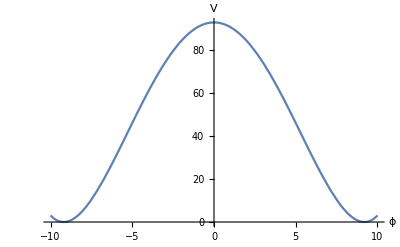

PASSED

ϕ0list = {-10.721,-9.19866,-9.19866,-7.89253,7.89253,9.19866,9.19866,10.721}

vacuumArray = {9.19866,9.19866}

ϕi1s = {0.124444}

{80.}

{a,b,c,Z} = -0.022, 0, 0.00013, 0

{-72.8571,{x→12.5357}}

{a,b,c,g} = -0.022, 0, 0.00007, 1.72857

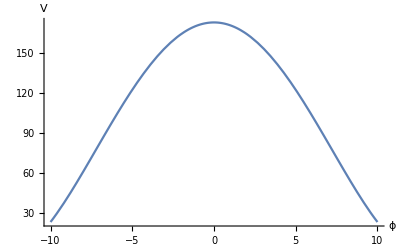

PASSED

ϕ0list = {-14.0294,-12.5357,-12.5357,-11.201,11.201,12.5357,12.5357,14.0294}

vacuumArray = {12.5357,12.5357}

ϕi1s = {0.983654}

{80.}

{a,b,c,Z} = -0.022, 0, 0.00007, 0

{-33.1783,{x→-10.8698}}

{a,b,c,g} = -0.022, 0.0001, 1/10000, 1.33178

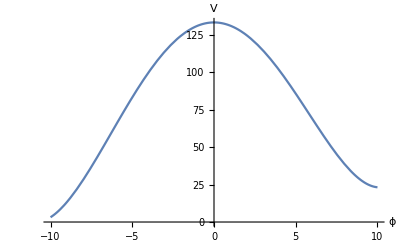

PASSED

ϕ0list = {-12.3768,-10.8698,-10.8698,-9.5482}

vacuumArray = {-10.8698,-10.8698}

ϕi1s = t

ABORTED

{-20.5292,{x→-10.3467}}

{a,b,c,g} = -0.022, 0.0001, 0.00011, 1.20529

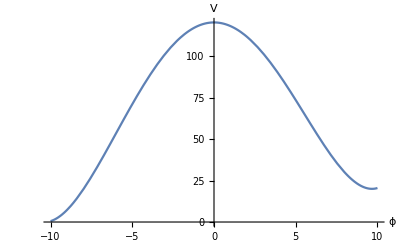

PASSED

ϕ0list = {-11.8583,-10.3467,-10.3467,-9.02972}

vacuumArray = {-10.3467,-10.3467}

ϕi1s = t

ABORTED

{-10.0538,{x→-9.89187}}

{a,b,c,g} = -0.022, 0.0001, 0.00012, 1.10054

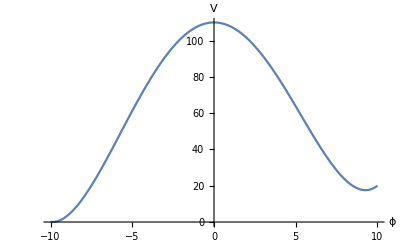

PASSED

ϕ0list = {-11.4078,-9.89187,-9.89187,-8.57924}

vacuumArray = {-9.89187,-9.89187}

ϕi1s = t

ABORTED

{-48.75,{x→-11.4799}}

{a,b,c,g} = -0.022, 0.0001, 0.00009, 1.4875

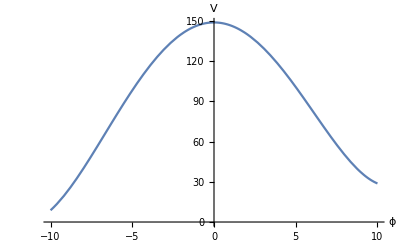

PASSED

ϕ0list = {-12.9821,-11.4799,-11.4799,-10.1535}

vacuumArray = {-11.4799,-11.4799}

ϕi1s = t

ABORTED

{-36.0559,{x→11.2667}}

{a,b,c,g} = -0.022, 0.0001, 0.00008, 1.36056

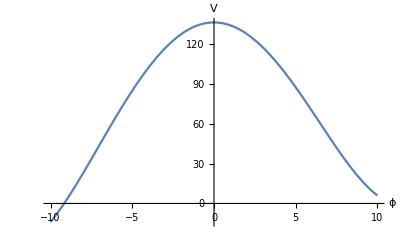

PASSED

ϕ0list = {-15.4649,-14.0293,-9.81997,-8.42701,9.93976,11.2667,11.2667,12.768}

vacuumArray = {11.2667,11.2667}

ϕi1s = {0.522284}

{80.}

{a,b,c,Z} = -0.022, 0.0001, 0.00008, 0

{-1.23825,{x→-9.49165}}

{a,b,c,g} = -0.022, 0.0001, 0.00013, 1.01238

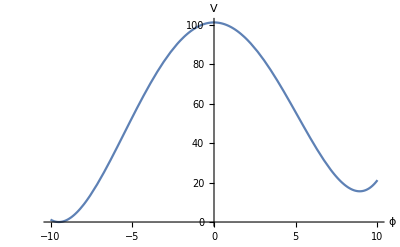

PASSED

ϕ0list = {-11.0118,-9.49165,-9.49165,-8.18321}

vacuumArray = {-9.49165,-9.49165}

ϕi1s = t

ABORTED

{-93.8743,{x→-13.0828}}

{a,b,c,g} = -0.022, 0.0001, 0.00007, 1.93874

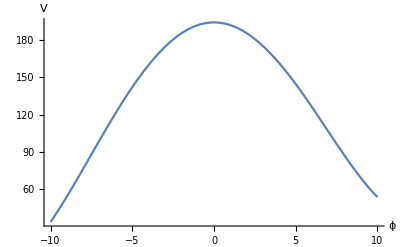

PASSED

ϕ0list = {-14.5744,-13.0828,-13.0828,-11.7458}

vacuumArray = {-13.0828,-13.0828}

ϕi1s = t

ABORTED

{-33.1783,{x→10.8698}}

{a,b,c,g} = -0.022, -0.0001, 1/10000, 1.33178

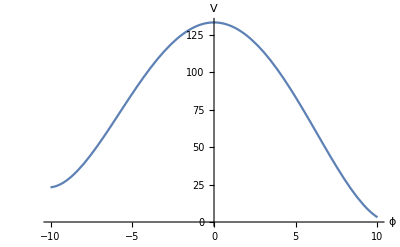

PASSED

ϕ0list = {9.5482,10.8698,10.8698,12.3768}

vacuumArray = {10.8698,10.8698}

ϕi1s = {0.449584}

{80.}

{a,b,c,Z} = -0.022, -0.0001, 1/10000, 0

{-20.5292,{x→10.3467}}

{a,b,c,g} = -0.022, -0.0001, 0.00011, 1.20529

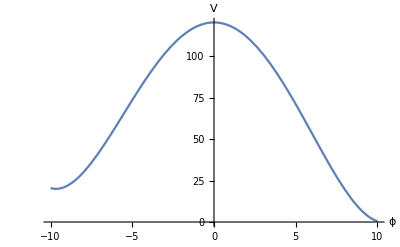

PASSED

ϕ0list = {9.02972,10.3467,10.3467,11.8583}

vacuumArray = {10.3467,10.3467}

ϕi1s = {0.323897}

{80.}

{a,b,c,Z} = -0.022, -0.0001, 0.00011, 0

{-10.0538,{x→9.89187}}

{a,b,c,g} = -0.022, -0.0001, 0.00012, 1.10054

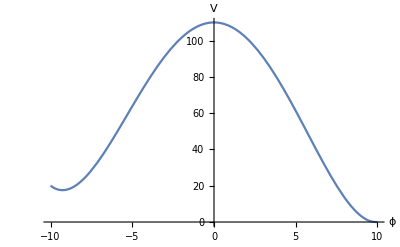

PASSED

ϕ0list = {8.57924,9.89187,9.89187,11.4078}

vacuumArray = {9.89187,9.89187}

ϕi1s = {0.234273}

{80.}

{a,b,c,Z} = -0.022, -0.0001, 0.00012, 0

{-48.75,{x→11.4799}}

{a,b,c,g} = -0.022, -0.0001, 0.00009, 1.4875

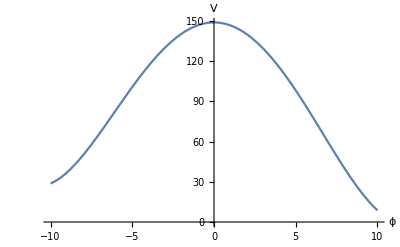

PASSED

ϕ0list = {10.1535,11.4799,11.4799,12.9821}

vacuumArray = {11.4799,11.4799}

ϕi1s = {0.62714}

{80.}

{a,b,c,Z} = -0.022, -0.0001, 0.00009, 0

{-68.3798,{x→12.2042}}

{a,b,c,g} = -0.022, -0.0001, 0.00008, 1.6838

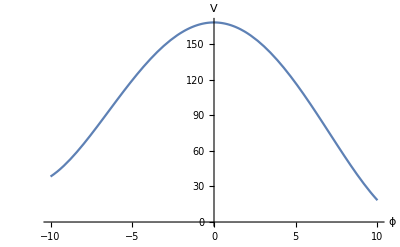

PASSED

ϕ0list = {10.8726,12.2042,12.2042,13.7012}

vacuumArray = {12.2042,12.2042}

ϕi1s = {0.880392}

{80.}

{a,b,c,Z} = -0.022, -0.0001, 0.00008, 0

{-1.23825,{x→9.49165}}

{a,b,c,g} = -0.022, -0.0001, 0.00013, 1.01238

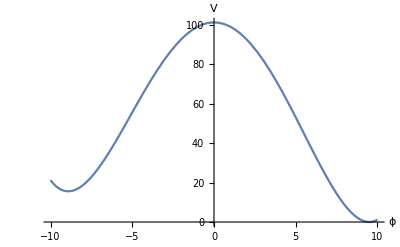

PASSED

ϕ0list = {8.18321,9.49165,9.49165,11.0118}

vacuumArray = {9.49165,9.49165}

ϕi1s = {0.169996}

{80.}

{a,b,c,Z} = -0.022, -0.0001, 0.00013, 0

{-93.8743,{x→13.0828}}

{a,b,c,g} = -0.022, -0.0001, 0.00007, 1.93874

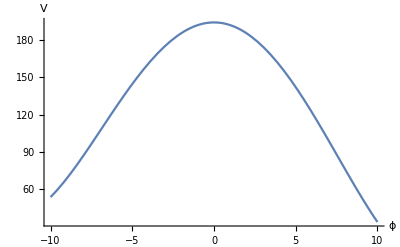

PASSED

ϕ0list = {11.7458,13.0828,13.0828,14.5744}

vacuumArray = {13.0828,13.0828}

ϕi1s = {1.24634}

{80.}

{a,b,c,Z} = -0.022, -0.0001, 0.00007, 0

{-226.333,{x→-14.8883}}

{a,b,c,g} = -0.022, 0.001, 1/10000, 3.26333

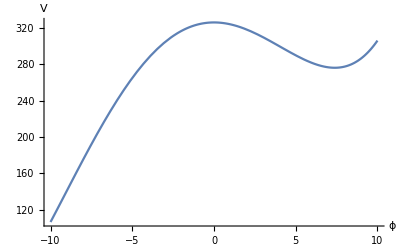

PASSED

ϕ0list = {-16.3774,-14.8883,-14.8883,-13.5483}

vacuumArray = {-14.8883,-14.8883}

ϕi1s = t

ABORTED

{-183.028,{x→-13.9742}}

{a,b,c,g} = -0.022, 0.001, 0.00011, 2.83028

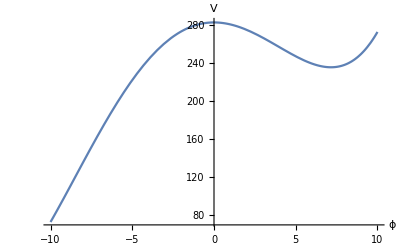

PASSED

ϕ0list = {-15.4678,-13.9742,-13.9742,-12.6387}

vacuumArray = {-13.9742,-13.9742}

ϕi1s = t

ABORTED

{-149.01,{x→-13.1964}}

{a,b,c,g} = -0.022, 0.001, 0.00012, 2.4901

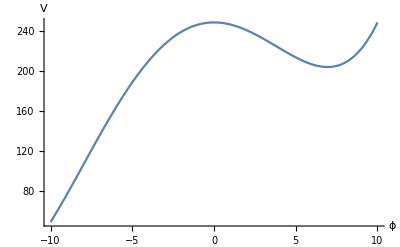

PASSED

ϕ0list = {-14.6943,-13.1964,-13.1964,-11.8651}

vacuumArray = {-13.1964,-13.1964}

ϕi1s = t

ABORTED

{-282.978,{x→-15.9812}}

{a,b,c,g} = -0.022, 0.001, 0.00009, 3.82978

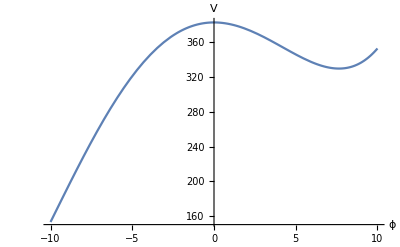

PASSED

ϕ0list = {-17.4655,-15.9812,-15.9812,-14.6365}

vacuumArray = {-15.9812,-15.9812}

ϕi1s = t

ABORTED

{-359.615,{x→-17.3157}}

{a,b,c,g} = -0.022, 0.001, 0.00008, 4.59615

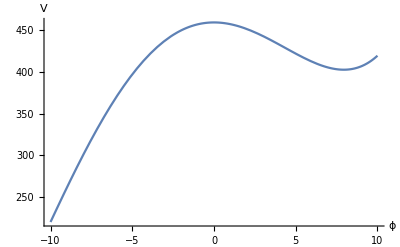

PASSED

ϕ0list = {-18.795,-17.3157,-17.3157,-15.966}

vacuumArray = {-17.3157,-17.3157}

ϕi1s = t

ABORTED

{-121.684,{x→-12.525}}

{a,b,c,g} = -0.022, 0.001, 0.00013, 2.21684

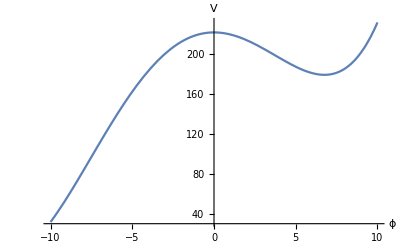

PASSED

ϕ0list = {-14.027,-12.525,-12.525,-11.1978}

vacuumArray = {-12.525,-12.525}

ϕi1s = t

ABORTED

{-467.854,{x→-18.9895}}

{a,b,c,g} = -0.022, 0.001, 0.00007, 5.67854

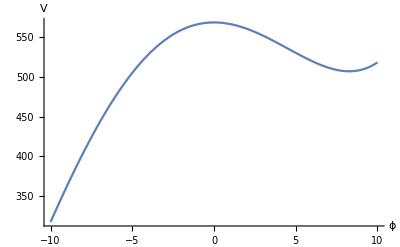

PASSED

ϕ0list = {-20.4634,-18.9895,-18.9895,-17.6345}

vacuumArray = {-18.9895,-18.9895}

ϕi1s = t

ABORTED

{-226.333,{x→14.8883}}

{a,b,c,g} = -0.022, -0.001, 1/10000, 3.26333

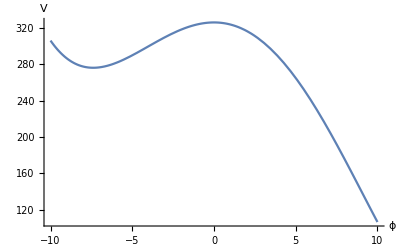

PASSED

ϕ0list = {13.5483,14.8883,14.8883,16.3774}

vacuumArray = {14.8883,14.8883}

ϕi1s = {2.44527}

{80.}

{a,b,c,Z} = -0.022, -0.001, 1/10000, 0

{-183.028,{x→13.9742}}

{a,b,c,g} = -0.022, -0.001, 0.00011, 2.83028

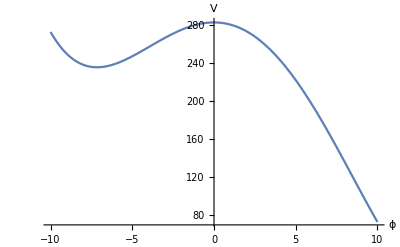

PASSED

ϕ0list = {12.6387,13.9742,13.9742,15.4678}

vacuumArray = {13.9742,13.9742}

ϕi1s = {1.92526}

{80.}

{a,b,c,Z} = -0.022, -0.001, 0.00011, 0

{-149.01,{x→13.1964}}

{a,b,c,g} = -0.022, -0.001, 0.00012, 2.4901

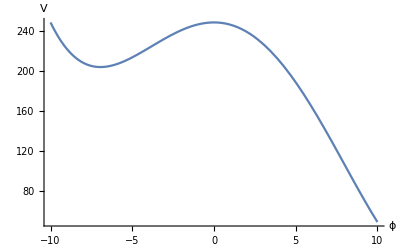

PASSED

ϕ0list = {11.8651,13.1964,13.1964,14.6943}

vacuumArray = {13.1964,13.1964}

ϕi1s = {1.52251}

{80.}

{a,b,c,Z} = -0.022, -0.001, 0.00012, 0

{-282.978,{x→15.9812}}

{a,b,c,g} = -0.022, -0.001, 0.00009, 3.82978

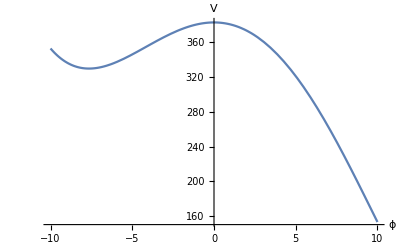

PASSED

ϕ0list = {14.6365,15.9812,15.9812,17.4655}

vacuumArray = {15.9812,15.9812}

ϕi1s = {3.12432}

{80.}

{a,b,c,Z} = -0.022, -0.001, 0.00009, 0

{-359.615,{x→17.3157}}

{a,b,c,g} = -0.022, -0.001, 0.00008, 4.59615

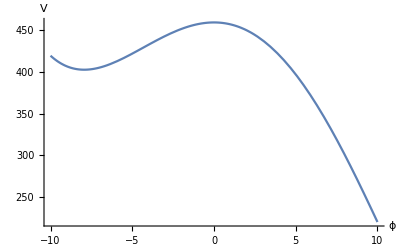

PASSED

ϕ0list = {15.966,17.3157,17.3157,18.795}

vacuumArray = {17.3157,17.3157}

ϕi1s = {4.02452}

{80.}

{a,b,c,Z} = -0.022, -0.001, 0.00008, 0

{-121.684,{x→12.525}}

{a,b,c,g} = -0.022, -0.001, 0.00013, 2.21684

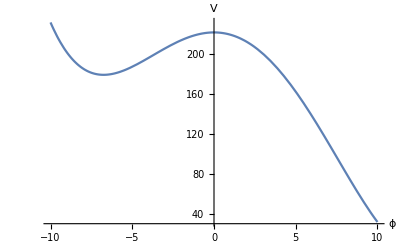

PASSED

ϕ0list = {11.1978,12.525,12.525,14.027}

vacuumArray = {12.525,12.525}

ϕi1s = {1.20789}

{80.}

{a,b,c,Z} = -0.022, -0.001, 0.00013, 0

{-467.854,{x→18.9895}}

{a,b,c,g} = -0.022, -0.001, 0.00007, 5.67854

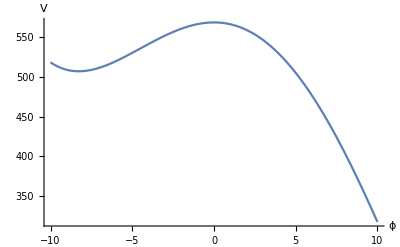

PASSED

ϕ0list = {17.6345,18.9895,18.9895,20.4634}

vacuumArray = {18.9895,18.9895}

ϕi1s = {5.24246}

{80.}

{a,b,c,Z} = -0.022, -0.001, 0.00007, 0

{-97.2702,{x→-12.5294}}

{a,b,c,g} = -0.022, 0.0005, 1/10000, 1.9727

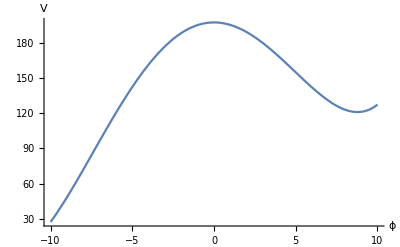

PASSED

ϕ0list = {-14.028,-12.5294,-12.5294,-11.1991}

vacuumArray = {-12.5294,-12.5294}

ϕi1s = t

ABORTED

{-75.2266,{x→-11.8488}}

{a,b,c,g} = -0.022, 0.0005, 0.00011, 1.75227

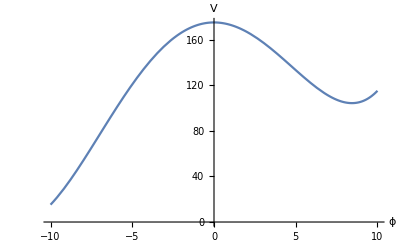

PASSED

ϕ0list = {-13.352,-11.8488,-11.8488,-10.5231}

vacuumArray = {-11.8488,-11.8488}

ϕi1s = t

ABORTED

{-57.4131,{x→-11.2634}}

{a,b,c,g} = -0.022, 0.0005, 0.00012, 1.57413

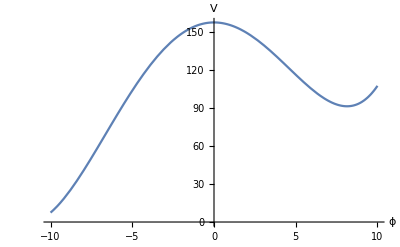

PASSED

ϕ0list = {-12.7711,-11.2634,-11.2634,-9.94208}

vacuumArray = {-11.2634,-11.2634}

ϕi1s = t

ABORTED

{-125.185,{x→-13.3333}}

{a,b,c,g} = -0.022, 0.0005, 0.00009, 2.25185

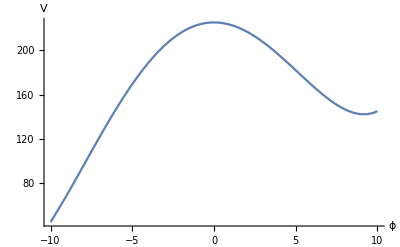

PASSED

ϕ0list = {-14.8272,-13.3333,-13.3333,-11.9983}

vacuumArray = {-13.3333,-13.3333}

ϕi1s = t

ABORTED

{-161.559,{x→-14.3017}}

{a,b,c,g} = -0.022, 0.0005, 0.00008, 2.61559

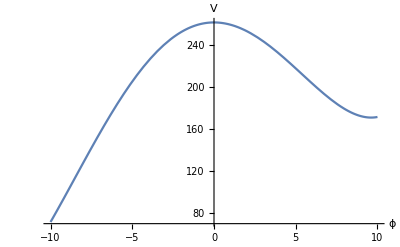

PASSED

ϕ0list = {-15.7904,-14.3017,-14.3017,-12.9616}

vacuumArray = {-14.3017,-14.3017}

ϕi1s = t

ABORTED

{-42.7414,{x→-10.7534}}

{a,b,c,g} = -0.022, 0.0005, 0.00013, 1.42741

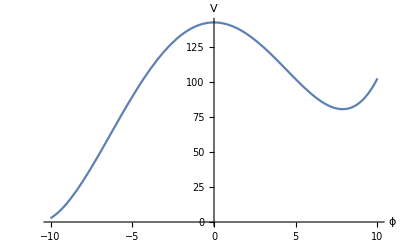

PASSED

ϕ0list = {-12.2652,-10.7534,-10.7534,-9.43618}

vacuumArray = {-10.7534,-10.7534}

ϕi1s = t

ABORTED

{-210.703,{x→-15.4972}}

{a,b,c,g} = -0.022, 0.0005, 0.00007, 3.10703

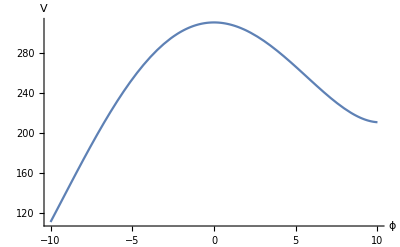

PASSED

ϕ0list = {-16.9805,-15.4972,-15.4972,-14.1517}

vacuumArray = {-15.4972,-15.4972}

ϕi1s = t

ABORTED

{-97.2702,{x→12.5294}}

{a,b,c,g} = -0.022, -0.0005, 1/10000, 1.9727

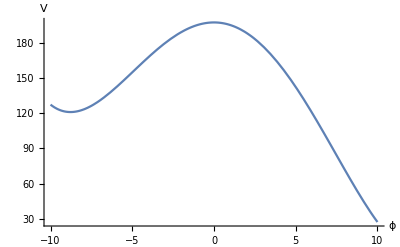

PASSED

ϕ0list = {11.1991,12.5294,12.5294,14.028}

vacuumArray = {12.5294,12.5294}

ϕi1s = {1.10735}

{80.}

{a,b,c,Z} = -0.022, -0.0005, 1/10000, 0

{-75.2266,{x→11.8488}}

{a,b,c,g} = -0.022, -0.0005, 0.00011, 1.75227

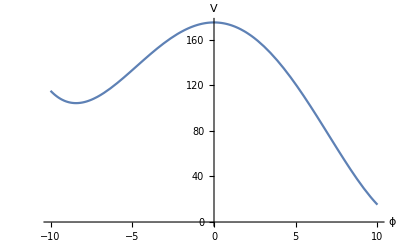

PASSED

ϕ0list = {10.5231,11.8488,11.8488,13.352}

vacuumArray = {11.8488,11.8488}

ϕi1s = {0.834967}

{80.}

{a,b,c,Z} = -0.022, -0.0005, 0.00011, 0

{-57.4131,{x→11.2634}}

{a,b,c,g} = -0.022, -0.0005, 0.00012, 1.57413

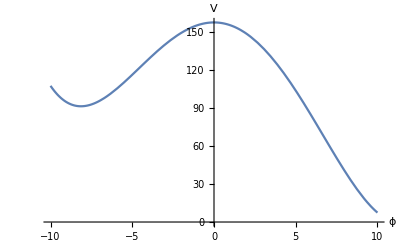

PASSED

ϕ0list = {9.94208,11.2634,11.2634,12.7711}

vacuumArray = {11.2634,11.2634}

ϕi1s = {0.631814}

{80.}

{a,b,c,Z} = -0.022, -0.0005, 0.00012, 0

{-125.185,{x→13.3333}}

{a,b,c,g} = -0.022, -0.0005, 0.00009, 2.25185

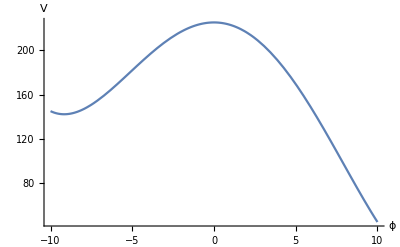

PASSED

ϕ0list = {11.9983,13.3333,13.3333,14.8272}

vacuumArray = {13.3333,13.3333}

ϕi1s = {1.47565}

{80.}

{a,b,c,Z} = -0.022, -0.0005, 0.00009, 0

{-161.559,{x→14.3017}}

{a,b,c,g} = -0.022, -0.0005, 0.00008, 2.61559

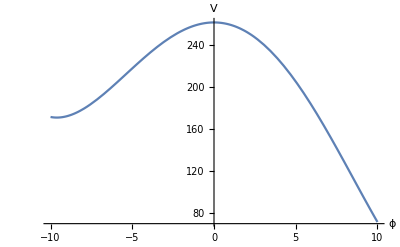

PASSED

ϕ0list = {12.9616,14.3017,14.3017,15.7904}

vacuumArray = {14.3017,14.3017}

ϕi1s = {1.97945}

{80.}

{a,b,c,Z} = -0.022, -0.0005, 0.00008, 0

{-42.7414,{x→10.7534}}

{a,b,c,g} = -0.022, -0.0005, 0.00013, 1.42741

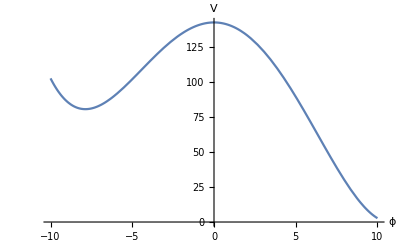

PASSED

ϕ0list = {9.43618,10.7534,10.7534,12.2652}

vacuumArray = {10.7534,10.7534}

ϕi1s = {0.479348}

{80.}

{a,b,c,Z} = -0.022, -0.0005, 0.00013, 0

{-210.703,{x→15.4972}}

{a,b,c,g} = -0.022, -0.0005, 0.00007, 3.10703

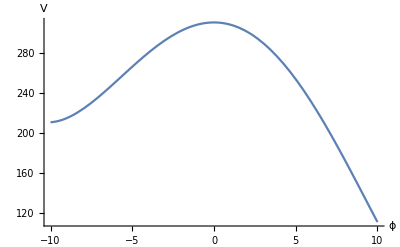

PASSED

ϕ0list = {14.1517,15.4972,15.4972,16.9805}

vacuumArray = {15.4972,15.4972}

ϕi1s = {2.67977}

{80.}

{a,b,c,Z} = -0.022, -0.0005, 0.00007, 0

{100.,{x→3.70577×10^-21}}

{100.,{x→4.12929×10^-21}}

{100.,{x→4.44692×10^-21}}

{100.,{x→3.38813×10^-21}}

{100.,{x→2.96462×10^-21}}

{100.,{x→4.87044×10^-21}}

{100.,{x→2.64698×10^-21}}

{100.,{x→2.37816×10^-15}}

{100.,{x→2.37816×10^-15}}

{100.,{x→2.37816×10^-15}}

«4 more identical outputs»

{100.,{x→-2.37815×10^-15}}

{100.,{x→-2.37815×10^-15}}

{100.,{x→-2.37815×10^-15}}

{100.,{x→-2.37816×10^-15}}

{100.,{x→-2.37816×10^-15}}

{100.,{x→-2.37815×10^-15}}

{100.,{x→-2.37816×10^-15}}

{100.,{x→3.78653×10^-29}}

{100.,{x→3.78653×10^-29}}

{100.,{x→3.78653×10^-29}}

{100.,{x→4.10208×10^-29}}

{100.,{x→3.78653×10^-29}}

{100.,{x→3.78653×10^-29}}

{100.,{x→4.10208×10^-29}}

{100.,{x→-4.10208×10^-29}}

{100.,{x→-3.78653×10^-29}}

{100.,{x→-3.78653×10^-29}}

{100.,{x→-3.78653×10^-29}}

{100.,{x→-4.10208×10^-29}}

{100.,{x→-3.78653×10^-29}}

{100.,{x→-3.78653×10^-29}}

{100.,{x→4.73317×10^-30}}

{100.,{x→6.31089×10^-30}}

{100.,{x→6.31089×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→4.73317×10^-30}}

«1 more identical outputs»

{100.,{x→-4.73317×10^-30}}

{100.,{x→-4.73317×10^-30}}

{100.,{x→-4.73317×10^-30}}

«3 more identical outputs»

{100.,{x→-3.15544×10^-30}}

{19.,{x→-9.48683}}

{a,b,c,g} = -0.018, 0, 1/10000, 0.81

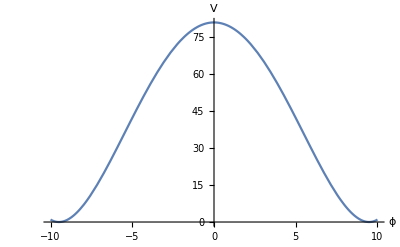

PASSED

ϕ0list = {-11.0059,-9.48683,-8.17745,8.17745,9.48683,11.0059}

vacuumArray = {9.48683}

ϕi1s = {0.161131}

{80.}

{a,b,c,Z} = -0.018, 0, 1/10000, 0

{26.3636,{x→9.04534}}

{a,b,c,g} = -0.018, 0, 0.00011, 0.736364

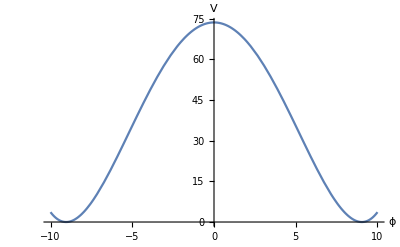

PASSED

ϕ0list = {-10.5694,-9.04534,-9.04534,-7.74101,7.74101,9.04534,9.04534,10.5694}

vacuumArray = {9.04534,9.04534}

ϕi1s = {0.107453}

{80.}

{a,b,c,Z} = -0.018, 0, 0.00011, 0

{32.5,{x→8.66025}}

{a,b,c,g} = -0.018, 0, 0.00012, 0.675

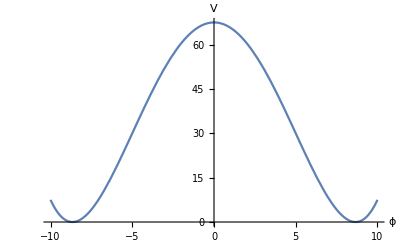

PASSED

ϕ0list = {-10.1892,-8.66025,-8.66025,-7.36075,7.36075,8.66025,8.66025,10.1892}

vacuumArray = {8.66025,8.66025}

ϕi1s = {0.0719579}

{80.}

{a,b,c,Z} = -0.018, 0, 0.00012, 0

{10.,{x→10.}}

{a,b,c,g} = -0.018, 0, 0.00009, 0.9

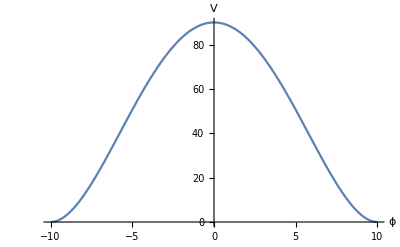

PASSED

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

vacuumArray = {10.,10.}

ϕi1s = {0.242866}

{80.}

{a,b,c,Z} = -0.018, 0, 0.00009, 0

{-1.25,{x→10.6066}}

{a,b,c,g} = -0.018, 0, 0.00008, 1.0125

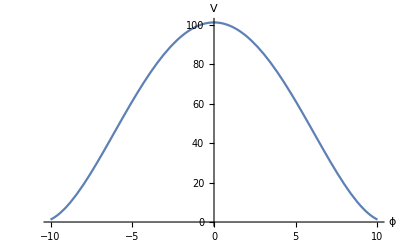

PASSED

ϕ0list = {-12.1147,-10.6066,-9.28625,9.28625,10.6066,12.1147}

vacuumArray = {10.6066}

ϕi1s = {0.368406}

{80.}

{a,b,c,Z} = -0.018, 0, 0.00008, 0

{37.6923,{x→8.3205}}

{a,b,c,g} = -0.018, 0, 0.00013, 0.623077

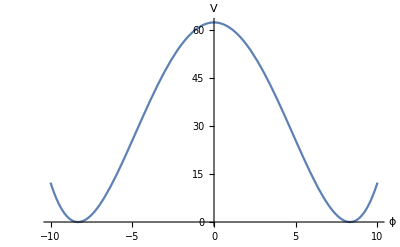

PASSED

ϕ0list = {-9.85405,-8.3205,-8.3205,-7.02562,7.02562,8.3205,8.3205,9.85405}

vacuumArray = {8.3205,8.3205}

ϕi1s = {0.0483579}

{80.}

{a,b,c,Z} = -0.018, 0, 0.00013, 0

{-15.7143,{x→-11.3389}}

{a,b,c,g} = -0.018, 0, 0.00007, 1.15714

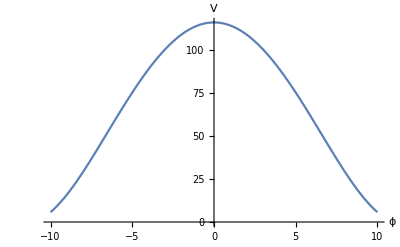

PASSED

ϕ0list = {-12.841,-11.3389,-11.3389,-10.0126,10.0126,11.3389,11.3389,12.841}

vacuumArray = {11.3389,11.3389}

ϕi1s = {0.563448}

{80.}

{a,b,c,Z} = -0.018, 0, 0.00007, 0

{9.93505,{x→-9.86924}}

{a,b,c,g} = -0.018, 0.0001, 1/10000, 0.900649

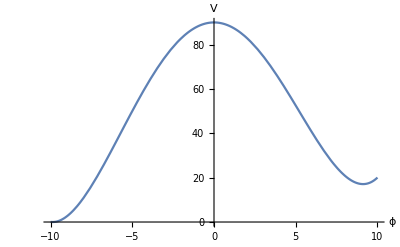

PASSED

ϕ0list = {-11.3857,-9.86924,-9.86924,-8.55706}

vacuumArray = {-9.86924,-9.86924}

ϕi1s = t

ABORTED

{18.5283,{x→-9.39267}}

{a,b,c,g} = -0.018, 0.0001, 0.00011, 0.814717

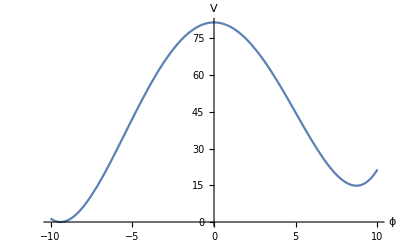

PASSED

ϕ0list = {-10.9142,-9.39267,-9.39267,-8.08554}

vacuumArray = {-9.39267,-9.39267}

ϕi1s = t

ABORTED

{25.6403,{x→-8.97839}}

{a,b,c,g} = -0.018, 0.0001, 0.00012, 0.743597

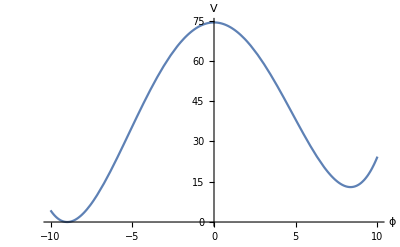

PASSED

ϕ0list = {-10.5047,-8.97839,-8.97839,-7.67609}

vacuumArray = {-8.97839,-8.97839}

ϕi1s = t

ABORTED

{-0.651776,{x→-10.4253}}

{a,b,c,g} = -0.018, 0.0001, 0.00009, 1.00652

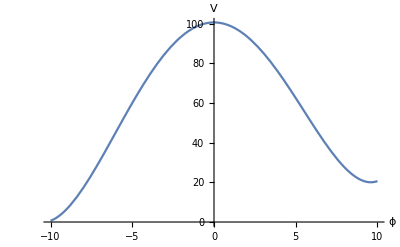

PASSED

ϕ0list = {-11.9364,-10.4253,-10.4253,-9.10784}

vacuumArray = {-10.4253,-10.4253}

ϕi1s = t

ABORTED

{-14.0094,{x→-11.0857}}

{a,b,c,g} = -0.018, 0.0001, 0.00008, 1.14009

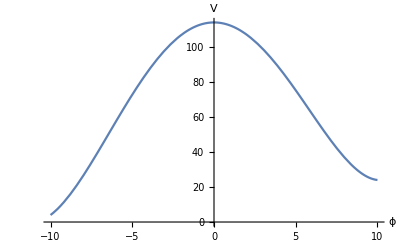

PASSED

ϕ0list = {-12.5912,-11.0857,-11.0857,-9.76256}

vacuumArray = {-11.0857,-11.0857}

ϕi1s = t

ABORTED

{31.6218,{x→-8.61396}}

{a,b,c,g} = -0.018, 0.0001, 0.00013, 0.683782

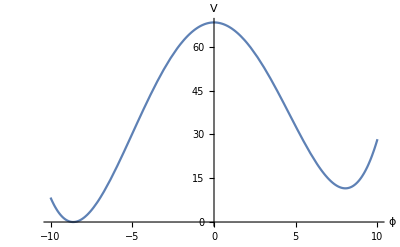

PASSED

ϕ0list = {-10.1449,-8.61396,-8.61396,-7.31628}

vacuumArray = {-8.61396,-8.61396}

ϕi1s = t

ABORTED

{-31.3765,{x→-11.8873}}

{a,b,c,g} = -0.018, 0.0001, 0.00007, 1.31376

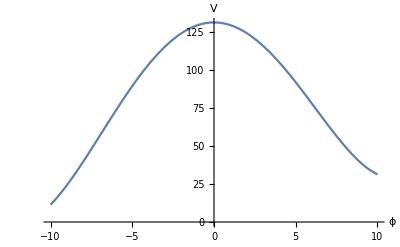

PASSED

ϕ0list = {-13.3867,-11.8873,-11.8873,-10.5581}

vacuumArray = {-11.8873,-11.8873}

ϕi1s = t

ABORTED

{9.93505,{x→9.86924}}

{a,b,c,g} = -0.018, -0.0001, 1/10000, 0.900649

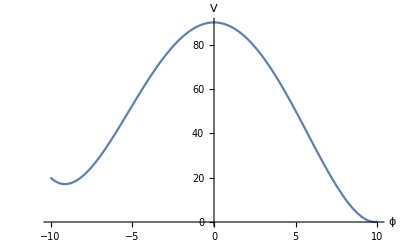

PASSED

ϕ0list = {8.55706,9.86924,9.86924,11.3857}

vacuumArray = {9.86924,9.86924}

ϕi1s = {0.23256}

{80.}

{a,b,c,Z} = -0.018, -0.0001, 1/10000, 0

{18.5283,{x→9.39267}}

{a,b,c,g} = -0.018, -0.0001, 0.00011, 0.814717

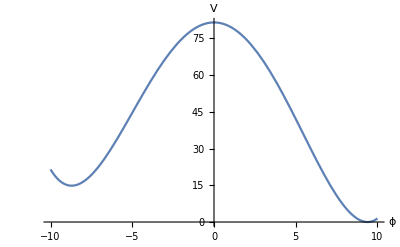

PASSED

ϕ0list = {8.08554,9.39267,9.39267,10.9142}

vacuumArray = {9.39267,9.39267}

ϕi1s = {0.157824}

{80.}

{a,b,c,Z} = -0.018, -0.0001, 0.00011, 0

{25.6403,{x→8.97839}}

{a,b,c,g} = -0.018, -0.0001, 0.00012, 0.743597

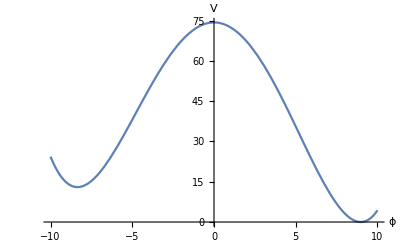

PASSED

ϕ0list = {7.67609,8.97839,8.97839,10.5047}

vacuumArray = {8.97839,8.97839}

ϕi1s = {0.107494}

{80.}

{a,b,c,Z} = -0.018, -0.0001, 0.00012, 0

{-0.651776,{x→10.4253}}

{a,b,c,g} = -0.018, -0.0001, 0.00009, 1.00652

-Graphics-

PASSED

ϕ0list = {9.10784,10.4253,10.4253,11.9364}

vacuumArray = {10.4253,10.4253}

ϕi1s = {0.344247}

{80.}

{a,b,c,Z} = -0.018, -0.0001, 0.00009, 0

{-14.0094,{x→11.0857}}

{a,b,c,g} = -0.018, -0.0001, 0.00008, 1.14009

-Graphics-

PASSED

ϕ0list = {9.76256,11.0857,12.5912}

vacuumArray = {11.0857}

ϕi1s = {0.512555}

{80.}

{a,b,c,Z} = -0.018, -0.0001, 0.00008, 0

{31.6218,{x→8.61396}}

{a,b,c,g} = -0.018, -0.0001, 0.00013, 0.683782

-Graphics-

PASSED

ϕ0list = {7.31628,8.61396,8.61396,10.1449}

vacuumArray = {8.61396,8.61396}

ϕi1s = {0.0734323}

{80.}

{a,b,c,Z} = -0.018, -0.0001, 0.00013, 0

{-31.3765,{x→11.8873}}

{a,b,c,g} = -0.018, -0.0001, 0.00007, 1.31376

-Graphics-

PASSED

ϕ0list = {10.5581,11.8873,11.8873,13.3867}

vacuumArray = {11.8873,11.8873}

ϕi1s = {0.769095}

{80.}

{a,b,c,Z} = -0.018, -0.0001, 0.00007, 0

{-143.054,{x→-13.9511}}

{a,b,c,g} = -0.018, 0.001, 1/10000, 2.43054

-Graphics-

PASSED

ϕ0list = {-15.4459,-13.9511,-13.9511,-12.6167}

vacuumArray = {-13.9511,-13.9511}

ϕi1s = t

ABORTED

{-109.761,{x→-13.0755}}

{a,b,c,g} = -0.018, 0.001, 0.00011, 2.09761

-Graphics-

PASSED

ϕ0list = {-14.5753,-13.0755,-13.0755,-11.7461}

vacuumArray = {-13.0755,-13.0755}

ϕi1s = t

ABORTED

{-83.7502,{x→-12.3318}}

{a,b,c,g} = -0.018, 0.001, 0.00012, 1.8375

-Graphics-

PASSED

ϕ0list = {-13.8364,-12.3318,-12.3318,-11.0071}

vacuumArray = {-12.3318,-12.3318}

ϕi1s = t

ABORTED

{-186.875,{x→-15.}}

{a,b,c,g} = -0.018, 0.001, 0.00009, 2.86875

-Graphics-

PASSED

ϕ0list = {-16.4896,-15.,-15.,-13.6604}

vacuumArray = {-15.,-15.}

ϕi1s = t

ABORTED

{-246.589,{x→-16.2837}}

{a,b,c,g} = -0.018, 0.001, 0.00008, 3.46589

-Graphics-

PASSED

ϕ0list = {-17.7678,-16.2837,-16.2837,-14.9387}

vacuumArray = {-16.2837,-16.2837}

ϕi1s = t

ABORTED

{-62.9584,{x→-11.691}}

{a,b,c,g} = -0.018, 0.001, 0.00013, 1.62958

-Graphics-

PASSED

ϕ0list = {-13.2001,-11.691,-11.691,-10.3707}

vacuumArray = {-11.691,-11.691}

ϕi1s = t

ABORTED

{-331.634,{x→-17.8979}}

{a,b,c,g} = -0.018, 0.001, 0.00007, 4.31634

-Graphics-

PASSED

ϕ0list = {-19.3761,-17.8979,-17.8979,-16.5471}

vacuumArray = {-17.8979,-17.8979}

ϕi1s = t

ABORTED

{-143.054,{x→13.9511}}

{a,b,c,g} = -0.018, -0.001, 1/10000, 2.43054

-Graphics-

PASSED

ϕ0list = {12.6167,13.9511,13.9511,15.4459}

vacuumArray = {13.9511,13.9511}

ϕi1s = {1.95849}

{80.}

{a,b,c,Z} = -0.018, -0.001, 1/10000, 0

{-109.761,{x→13.0755}}

{a,b,c,g} = -0.018, -0.001, 0.00011, 2.09761

-Graphics-

PASSED

ϕ0list = {11.7461,13.0755,13.0755,14.5753}

vacuumArray = {13.0755,13.0755}

ϕi1s = {1.50577}

{80.}

{a,b,c,Z} = -0.018, -0.001, 0.00011, 0

{-83.7502,{x→12.3318}}

{a,b,c,g} = -0.018, -0.001, 0.00012, 1.8375

-Graphics-

PASSED

ϕ0list = {11.0071,12.3318,12.3318,13.8364}

vacuumArray = {12.3318,12.3318}

ϕi1s = {1.16181}

{80.}

{a,b,c,Z} = -0.018, -0.001, 0.00012, 0

{-186.875,{x→15.}}

{a,b,c,g} = -0.018, -0.001, 0.00009, 2.86875

-Graphics-

PASSED

ϕ0list = {13.6604,15.,15.,16.4896}

vacuumArray = {15.,15.}

ϕi1s = {2.56054}

{80.}

{a,b,c,Z} = -0.018, -0.001, 0.00009, 0

{-246.589,{x→16.2837}}

{a,b,c,g} = -0.018, -0.001, 0.00008, 3.46589

-Graphics-

PASSED

ϕ0list = {14.9387,16.2837,16.2837,17.7678}

vacuumArray = {16.2837,16.2837}

ϕi1s = {3.3725}

{80.}

{a,b,c,Z} = -0.018, -0.001, 0.00008, 0

{-62.9584,{x→11.691}}

{a,b,c,g} = -0.018, -0.001, 0.00013, 1.62958

-Graphics-

PASSED

ϕ0list = {10.3707,11.691,11.691,13.2001}

vacuumArray = {11.691,11.691}

ϕi1s = {0.898533}

{80.}

{a,b,c,Z} = -0.018, -0.001, 0.00013, 0

{-331.634,{x→17.8979}}

{a,b,c,g} = -0.018, -0.001, 0.00007, 4.31634

-Graphics-

PASSED

ϕ0list = {16.5471,17.8979,17.8979,19.3761}

vacuumArray = {17.8979,17.8979}

ϕi1s = {4.48896}

{80.}

{a,b,c,Z} = -0.018, -0.001, 0.00007, 0

{-39.2023,{x→-11.5453}}

{a,b,c,g} = -0.018, 0.0005, 1/10000, 1.39202

-Graphics-

PASSED

ϕ0list = {-13.0517,-11.5453,-11.5453,-10.2226}

vacuumArray = {-11.5453,-11.5453}

ϕi1s = t

ABORTED

{-23.3358,{x→-10.9091}}

{a,b,c,g} = -0.018, 0.0005, 0.00011, 1.23336

-Graphics-

PASSED

ϕ0list = {-12.4205,-10.9091,-10.9091,-9.59141}

vacuumArray = {-10.9091,-10.9091}

ϕi1s = t

ABORTED

{-10.5543,{x→-10.3626}}

{a,b,c,g} = -0.018, 0.0005, 0.00012, 1.10554

-Graphics-

PASSED

ϕ0list = {-11.8788,-10.3626,-10.3626,-9.04969}

vacuumArray = {-10.3626,-10.3626}

ϕi1s = t

ABORTED

{-59.3674,{x→-12.298}}

{a,b,c,g} = -0.018, 0.0005, 0.00009, 1.59367

-Graphics-

PASSED

ϕ0list = {-13.7991,-12.298,-12.298,-10.9701}

vacuumArray = {-12.298,-12.298}

ϕi1s = t

ABORTED

{-85.754,{x→-13.2062}}

{a,b,c,g} = -0.018, 0.0005, 0.00008, 1.85754

-Graphics-

PASSED

ϕ0list = {-14.7016,-13.2062,-13.2062,-11.8726}

vacuumArray = {-13.2062,-13.2062}

ϕi1s = t

ABORTED

{-0.0562156,{x→-9.88689}}

{a,b,c,g} = -0.018, 0.0005, 0.00013, 1.00056

-Graphics-

PASSED

ϕ0list = {-11.4078,-9.88689,-9.88689,-8.5786}

vacuumArray = {-9.88689,-9.88689}

ϕi1s = t

ABORTED

{-121.583,{x→-14.3296}}

{a,b,c,g} = -0.018, 0.0005, 0.00007, 2.21583

-Graphics-

PASSED

ϕ0list = {-15.819,-14.3296,-14.3296,-12.9901}

vacuumArray = {-14.3296,-14.3296}

ϕi1s = t

ABORTED

{-39.2023,{x→11.5453}}

{a,b,c,g} = -0.018, -0.0005, 1/10000, 1.39202

-Graphics-

PASSED

ϕ0list = {10.2226,11.5453,11.5453,13.0517}

vacuumArray = {11.5453,11.5453}

ϕi1s = {0.745835}

{80.}

{a,b,c,Z} = -0.018, -0.0005, 1/10000, 0

{-23.3358,{x→10.9091}}

{a,b,c,g} = -0.018, -0.0005, 0.00011, 1.23336

-Graphics-

PASSED

ϕ0list = {9.59141,10.9091,10.9091,12.4205}

vacuumArray = {10.9091,10.9091}

ϕi1s = {0.539924}

{80.}

{a,b,c,Z} = -0.018, -0.0005, 0.00011, 0

{-10.5543,{x→10.3626}}

{a,b,c,g} = -0.018, -0.0005, 0.00012, 1.10554

-Graphics-

PASSED

ϕ0list = {9.04969,10.3626,10.3626,11.8788}

vacuumArray = {10.3626,10.3626}

ϕi1s = {0.39185}

{80.}

{a,b,c,Z} = -0.018, -0.0005, 0.00012, 0

{-59.3674,{x→12.298}}

{a,b,c,g} = -0.018, -0.0005, 0.00009, 1.59367

-Graphics-

PASSED

ϕ0list = {10.9701,12.298,12.298,13.7991}

vacuumArray = {12.298,12.298}

ϕi1s = {1.03411}

{80.}

{a,b,c,Z} = -0.018, -0.0005, 0.00009, 0

{-85.754,{x→13.2062}}

{a,b,c,g} = -0.018, -0.0005, 0.00008, 1.85754

-Graphics-

PASSED

ϕ0list = {11.8726,13.2062,13.2062,14.7016}

vacuumArray = {13.2062,13.2062}

ϕi1s = {1.44166}

{80.}

{a,b,c,Z} = -0.018, -0.0005, 0.00008, 0

{-0.0562156,{x→9.88689}}

{a,b,c,g} = -0.018, -0.0005, 0.00013, 1.00056

-Graphics-

PASSED

ϕ0list = {8.5786,9.88689,9.88689,11.4078}

vacuumArray = {9.88689,9.88689}

ϕi1s = {0.284866}

{80.}

{a,b,c,Z} = -0.018, -0.0005, 0.00013, 0

{-121.583,{x→14.3296}}

{a,b,c,g} = -0.018, -0.0005, 0.00007, 2.21583

-Graphics-

PASSED

ϕ0list = {12.9901,14.3296,14.3296,15.819}

vacuumArray = {14.3296,14.3296}

ϕi1s = {2.026}

{80.}

{a,b,c,Z} = -0.018, -0.0005, 0.00007, 0

{100.,{x→4.5528×10^-21}}

{100.,{x→5.0822×10^-21}}

{100.,{x→5.50571×10^-21}}

{100.,{x→4.12929×10^-21}}

{100.,{x→3.59989×10^-21}}

{100.,{x→5.92923×10^-21}}

{100.,{x→3.28225×10^-21}}

{100.,{x→2.90664×10^-15}}

{100.,{x→2.90664×10^-15}}

{100.,{x→2.90664×10^-15}}

«4 more identical outputs»

{100.,{x→-2.90663×10^-15}}

{100.,{x→-2.90663×10^-15}}

{100.,{x→-2.90663×10^-15}}

«4 more identical outputs»

{100.,{x→6.94198×10^-29}}

{100.,{x→6.94198×10^-29}}

{100.,{x→6.94198×10^-29}}

«4 more identical outputs»

{100.,{x→-6.94198×10^-29}}

{100.,{x→-6.94198×10^-29}}

{100.,{x→-6.94198×10^-29}}

«4 more identical outputs»

{100.,{x→9.46633×10^-30}}

{100.,{x→6.31089×10^-30}}

{100.,{x→9.46633×10^-30}}

{100.,{x→9.46633×10^-30}}

{100.,{x→9.46633×10^-30}}

{100.,{x→6.31089×10^-30}}

{100.,{x→9.46633×10^-30}}

{100.,{x→-9.46633×10^-30}}

{100.,{x→-9.46633×10^-30}}

{100.,{x→-9.46633×10^-30}}

«4 more identical outputs»

{-44.,{x→10.9545}}

{a,b,c,g} = -0.024, 0, 1/10000, 1.44

-Graphics-

PASSED

ϕ0list = {-12.4596,-10.9545,-10.9545,-9.63115,9.63115,10.9545,10.9545,12.4596}

vacuumArray = {10.9545,10.9545}

ϕi1s = {0.455073}

{80.}

{a,b,c,Z} = -0.024, 0, 1/10000, 0

{-30.9091,{x→10.4447}}

{a,b,c,g} = -0.024, 0, 0.00011, 1.30909

-Graphics-

PASSED

ϕ0list = {-11.9542,-10.4447,-10.4447,-9.12575,9.12575,10.4447,10.4447,11.9542}

vacuumArray = {10.4447,10.4447}

ϕi1s = {0.331733}

{80.}

{a,b,c,Z} = -0.024, 0, 0.00011, 0

{-20.,{x→10.}}

{a,b,c,g} = -0.024, 0, 0.00012, 1.2

-Graphics-

PASSED

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

vacuumArray = {10.,10.}

ϕi1s = {0.242866}

{80.}

{a,b,c,Z} = -0.024, 0, 0.00012, 0

{-60.,{x→-11.547}}

{a,b,c,g} = -0.024, 0, 0.00009, 1.6

-Graphics-

PASSED

ϕ0list = {-13.0475,-11.547,-11.547,-10.2191,10.2191,11.547,11.547,13.0475}

vacuumArray = {11.547,11.547}

ϕi1s = {0.627584}

{80.}

{a,b,c,Z} = -0.024, 0, 0.00009, 0

{-80.,{x→12.2474}}

{a,b,c,g} = -0.024, 0, 0.00008, 1.8

-Graphics-

PASSED

ϕ0list = {-13.743,-12.2474,-12.2474,-10.9146,10.9146,12.2474,12.2474,13.743}

vacuumArray = {12.2474,12.2474}

ϕi1s = {0.871276}

{80.}

{a,b,c,Z} = -0.024, 0, 0.00008, 0

{-10.7692,{x→-9.60769}}

{a,b,c,g} = -0.024, 0, 0.00013, 1.10769

-Graphics-

PASSED

ϕ0list = {-11.1254,-9.60769,-9.60769,-8.297,8.297,9.60769,9.60769,11.1254}

vacuumArray = {9.60769,9.60769}

ϕi1s = {0.178443}

{80.}

{a,b,c,Z} = -0.024, 0, 0.00013, 0

{-105.714,{x→-13.0931}}

{a,b,c,g} = -0.024, 0, 0.00007, 2.05714

-Graphics-

PASSED

ϕ0list = {-14.5834,-13.0931,-13.0931,-11.755,11.755,13.0931,13.0931,14.5834}

vacuumArray = {13.0931,13.0931}

ϕi1s = {1.2201}

{80.}

{a,b,c,Z} = -0.024, 0, 0.00007, 0

{-57.844,{x→-11.3359}}

{a,b,c,g} = -0.024, 0.0001, 1/10000, 1.57844

-Graphics-

PASSED

ϕ0list = {-12.839,-11.3359,-11.3359,-10.0105}

vacuumArray = {-11.3359,-11.3359}

ϕi1s = t

ABORTED

{-42.8797,{x→-10.7911}}

{a,b,c,g} = -0.024, 0.0001, 0.00011, 1.4288

-Graphics-

PASSED

ϕ0list = {-12.2987,-10.7911,-10.7911,-9.47012}

vacuumArray = {-10.7911,-10.7911}

ϕi1s = t

ABORTED

{-30.4837,{x→-10.3174}}

{a,b,c,g} = -0.024, 0.0001, 0.00012, 1.30484

-Graphics-

PASSED

ϕ0list = {-11.8291,-10.3174,-10.3174,-9.00057}

vacuumArray = {-10.3174,-10.3174}

ϕi1s = t

ABORTED

{-76.2601,{x→-11.9712}}

{a,b,c,g} = -0.024, 0.0001, 0.00009, 1.7626

-Graphics-

PASSED

ϕ0list = {-13.4697,-11.9712,-11.9712,-10.6412}

vacuumArray = {-11.9712,-11.9712}

ϕi1s = t

ABORTED

{-99.4673,{x→-12.7252}}

{a,b,c,g} = -0.024, 0.0001, 0.00008, 1.99467

-Graphics-

PASSED

ϕ0list = {-14.2188,-12.7252,-12.7252,-11.3902}

vacuumArray = {-12.7252,-12.7252}

ϕi1s = t

ABORTED

{-20.0495,{x→-9.90048}}

{a,b,c,g} = -0.024, 0.0001, 0.00013, 1.2005

-Graphics-

PASSED

ϕ0list = {-11.4163,-9.90048,-9.90048,-8.58769}

vacuumArray = {-9.90048,-9.90048}

ϕi1s = t

ABORTED

{-129.595,{x→-13.6397}}

{a,b,c,g} = -0.024, 0.0001, 0.00007, 2.29595

-Graphics-

PASSED

ϕ0list = {-15.1281,-13.6397,-13.6397,-12.2996}

vacuumArray = {-13.6397,-13.6397}

ϕi1s = t

ABORTED

{-57.844,{x→11.3359}}

{a,b,c,g} = -0.024, -0.0001, 1/10000, 1.57844

-Graphics-

PASSED

ϕ0list = {10.0105,11.3359,11.3359,12.839}

vacuumArray = {11.3359,11.3359}

ϕi1s = {0.580604}

{80.}

{a,b,c,Z} = -0.024, -0.0001, 1/10000, 0

{-42.8797,{x→10.7911}}

{a,b,c,g} = -0.024, -0.0001, 0.00011, 1.4288

-Graphics-

PASSED

ϕ0list = {9.47012,10.7911,10.7911,12.2987}

vacuumArray = {10.7911,10.7911}

ϕi1s = {0.427792}

{80.}

{a,b,c,Z} = -0.024, -0.0001, 0.00011, 0

{-30.4837,{x→10.3174}}

{a,b,c,g} = -0.024, -0.0001, 0.00012, 1.30484

-Graphics-

PASSED

ϕ0list = {9.00057,10.3174,10.3174,11.8291}

vacuumArray = {10.3174,10.3174}

ϕi1s = {0.316492}

{80.}

{a,b,c,Z} = -0.024, -0.0001, 0.00012, 0

{-76.2601,{x→11.9712}}

{a,b,c,g} = -0.024, -0.0001, 0.00009, 1.7626

-Graphics-

PASSED

ϕ0list = {10.6412,11.9712,11.9712,13.4697}

vacuumArray = {11.9712,11.9712}

ϕi1s = {0.792042}

{80.}

{a,b,c,Z} = -0.024, -0.0001, 0.00009, 0

{-99.4673,{x→12.7252}}

{a,b,c,g} = -0.024, -0.0001, 0.00008, 1.99467

-Graphics-

PASSED

ϕ0list = {11.3902,12.7252,12.7252,14.2188}

vacuumArray = {12.7252,12.7252}

ϕi1s = {1.08759}

{80.}

{a,b,c,Z} = -0.024, -0.0001, 0.00008, 0

{-20.0495,{x→9.90048}}

{a,b,c,g} = -0.024, -0.0001, 0.00013, 1.2005

-Graphics-

PASSED

ϕ0list = {8.58769,9.90048,9.90048,11.4163}

vacuumArray = {9.90048,9.90048}

ϕi1s = {0.234932}

{80.}

{a,b,c,Z} = -0.024, -0.0001, 0.00013, 0

{-129.595,{x→13.6397}}

{a,b,c,g} = -0.024, -0.0001, 0.00007, 2.29595

-Graphics-

PASSED

ϕ0list = {12.2996,13.6397,13.6397,15.1281}

vacuumArray = {13.6397,13.6397}

ϕi1s = {1.50641}

{80.}

{a,b,c,Z} = -0.024, -0.0001, 0.00007, 0

{-271.998,{x→-15.3285}}

{a,b,c,g} = -0.024, 0.001, 1/10000, 3.71998

-Graphics-

PASSED

ϕ0list = {-16.8151,-15.3285,-15.3285,-13.9861}

vacuumArray = {-15.3285,-15.3285}

ϕi1s = t

ABORTED

{-223.283,{x→-14.396}}

{a,b,c,g} = -0.024, 0.001, 0.00011, 3.23283

-Graphics-

PASSED

ϕ0list = {-15.887,-14.396,-14.396,-13.0579}

vacuumArray = {-14.396,-14.396}

ϕi1s = t

ABORTED

{-184.927,{x→-13.6019}}

{a,b,c,g} = -0.024, 0.001, 0.00012, 2.84927

-Graphics-

PASSED

ϕ0list = {-15.097,-13.6019,-13.6019,-12.2679}

vacuumArray = {-13.6019,-13.6019}

ϕi1s = t

ABORTED

{-335.556,{x→-16.4424}}

{a,b,c,g} = -0.024, 0.001, 0.00009, 4.35556

-Graphics-

PASSED

ϕ0list = {-17.9245,-16.4424,-16.4424,-15.0955}

vacuumArray = {-16.4424,-16.4424}

ϕi1s = t

ABORTED

{-421.291,{x→-17.8013}}

{a,b,c,g} = -0.024, 0.001, 0.00008, 5.21291

-Graphics-

PASSED

ϕ0list = {-19.2785,-17.8013,-17.8013,-16.4496}

vacuumArray = {-17.8013,-17.8013}

ϕi1s = t

ABORTED

{-154.055,{x→-12.916}}

{a,b,c,g} = -0.024, 0.001, 0.00013, 2.54055

-Graphics-

PASSED

ϕ0list = {-14.4151,-12.916,-12.916,-11.586}

vacuumArray = {-12.916,-12.916}

ϕi1s = t

ABORTED

{-541.957,{x→-19.5038}}

{a,b,c,g} = -0.024, 0.001, 0.00007, 6.41957

-Graphics-

PASSED

ϕ0list = {-20.9759,-19.5038,-19.5038,-18.147}

vacuumArray = {-19.5038,-19.5038}

ϕi1s = t

ABORTED

{-271.998,{x→15.3285}}

{a,b,c,g} = -0.024, -0.001, 1/10000, 3.71998

-Graphics-

PASSED

ϕ0list = {13.9861,15.3285,15.3285,16.8151}

vacuumArray = {15.3285,15.3285}

ϕi1s = {2.69179}

{80.}

{a,b,c,Z} = -0.024, -0.001, 1/10000, 0

{-223.283,{x→14.396}}

{a,b,c,g} = -0.024, -0.001, 0.00011, 3.23283

-Graphics-

PASSED

ϕ0list = {13.0579,14.396,14.396,15.887}

vacuumArray = {14.396,14.396}

ϕi1s = {2.14028}

{80.}

{a,b,c,Z} = -0.024, -0.001, 0.00011, 0

{-184.927,{x→13.6019}}

{a,b,c,g} = -0.024, -0.001, 0.00012, 2.84927

-Graphics-

PASSED

ϕ0list = {12.2679,13.6019,13.6019,15.097}

vacuumArray = {13.6019,13.6019}

ϕi1s = {1.70977}

{80.}

{a,b,c,Z} = -0.024, -0.001, 0.00012, 0

{-335.556,{x→16.4424}}

{a,b,c,g} = -0.024, -0.001, 0.00009, 4.35556

-Graphics-

PASSED

ϕ0list = {15.0955,16.4424,17.9245}

vacuumArray = {16.4424}

ϕi1s = {3.40663}

{80.}

{a,b,c,Z} = -0.024, -0.001, 0.00009, 0

{-421.291,{x→17.8013}}

{a,b,c,g} = -0.024, -0.001, 0.00008, 5.21291

-Graphics-

PASSED

ϕ0list = {16.4496,17.8013,17.8013,19.2785}

vacuumArray = {17.8013,17.8013}

ABORTED

{-154.055,{x→12.916}}

{a,b,c,g} = -0.024, -0.001, 0.00013, 2.54055

-Graphics-

PASSED

ϕ0list = {11.586,12.916,12.916,14.4151}

vacuumArray = {12.916,12.916}

ϕi1s = {1.37067}

{80.}

{a,b,c,Z} = -0.024, -0.001, 0.00013, 0

{-541.957,{x→19.5038}}

{a,b,c,g} = -0.024, -0.001, 0.00007, 6.41957

-Graphics-

PASSED

ϕ0list = {18.147,19.5038,19.5038,20.9759}

vacuumArray = {19.5038,19.5038}

ϕi1s = {5.61233}

{80.}

{a,b,c,Z} = -0.024, -0.001, 0.00007, 0

{-129.841,{x→-12.9888}}

{a,b,c,g} = -0.024, 0.0005, 1/10000, 2.29841

-Graphics-

PASSED

ϕ0list = {-14.4842,-12.9888,-12.9888,-11.6554}

vacuumArray = {-12.9888,-12.9888}

ϕi1s = t

ABORTED

{-104.365,{x→-12.2874}}

{a,b,c,g} = -0.024, 0.0005, 0.00011, 2.04365

-Graphics-

PASSED

ϕ0list = {-13.7873,-12.2874,-12.2874,-10.9584}

vacuumArray = {-12.2874,-12.2874}

ϕi1s = t

ABORTED

{-83.7517,{x→-11.6838}}

{a,b,c,g} = -0.024, 0.0005, 0.00012, 1.83752

-Graphics-

PASSED

ϕ0list = {-13.1879,-11.6838,-11.6838,-10.359}

vacuumArray = {-11.6838,-11.6838}

ϕi1s = t

ABORTED

{-162.055,{x→-13.8168}}

{a,b,c,g} = -0.024, 0.0005, 0.00009, 2.62055

-Graphics-

PASSED

ϕ0list = {-15.3076,-13.8168,-13.8168,-12.4788}

vacuumArray = {-13.8168,-13.8168}

ϕi1s = t

ABORTED

{-203.958,{x→-14.8134}}

{a,b,c,g} = -0.024, 0.0005, 0.00008, 3.03958

-Graphics-

PASSED

ϕ0list = {-16.2994,-14.8134,-14.8134,-13.4706}

vacuumArray = {-14.8134,-14.8134}

ϕi1s = t

ABORTED

{-66.755,{x→-11.1577}}

{a,b,c,g} = -0.024, 0.0005, 0.00013, 1.66755

-Graphics-

PASSED

ϕ0list = {-12.6658,-11.1577,-9.83682}

vacuumArray = {-11.1577}

ϕi1s = t

ABORTED

{-260.459,{x→-16.0428}}

{a,b,c,g} = -0.024, 0.0005, 0.00007, 3.60459

-Graphics-

PASSED

ϕ0list = {-17.5236,-16.0428,-16.0428,-14.6948}

vacuumArray = {-16.0428,-16.0428}

ϕi1s = t

ABORTED

{-129.841,{x→12.9888}}

{a,b,c,g} = -0.024, -0.0005, 1/10000, 2.29841

-Graphics-

PASSED

ϕ0list = {11.6554,12.9888,12.9888,14.4842}

vacuumArray = {12.9888,12.9888}

ϕi1s = {1.30161}

{80.}

{a,b,c,Z} = -0.024, -0.0005, 1/10000, 0

{-104.365,{x→12.2874}}

{a,b,c,g} = -0.024, -0.0005, 0.00011, 2.04365

-Graphics-

PASSED

ϕ0list = {10.9584,12.2874,12.2874,13.7873}

vacuumArray = {12.2874,12.2874}

ϕi1s = {0.997105}

{80.}

{a,b,c,Z} = -0.024, -0.0005, 0.00011, 0

{-83.7517,{x→11.6838}}

{a,b,c,g} = -0.024, -0.0005, 0.00012, 1.83752

-Graphics-

PASSED

ϕ0list = {10.359,11.6838,11.6838,13.1879}

vacuumArray = {11.6838,11.6838}

ϕi1s = {0.766813}

{80.}

{a,b,c,Z} = -0.024, -0.0005, 0.00012, 0

{-162.055,{x→13.8168}}

{a,b,c,g} = -0.024, -0.0005, 0.00009, 2.62055

-Graphics-

PASSED

ϕ0list = {12.4788,13.8168,13.8168,15.3076}

vacuumArray = {13.8168,13.8168}

ϕi1s = {1.7079}

{80.}

{a,b,c,Z} = -0.024, -0.0005, 0.00009, 0

{-203.958,{x→14.8134}}

{a,b,c,g} = -0.024, -0.0005, 0.00008, 3.03958

-Graphics-

PASSED

ϕ0list = {13.4706,14.8134,14.8134,16.2994}

vacuumArray = {14.8134,14.8134}

ϕi1s = {2.2567}

{80.}

{a,b,c,Z} = -0.024, -0.0005, 0.00008, 0

{-66.755,{x→11.1577}}

{a,b,c,g} = -0.024, -0.0005, 0.00013, 1.66755

-Graphics-

PASSED

ϕ0list = {9.83682,11.1577,11.1577,12.6658}

vacuumArray = {11.1577,11.1577}

ϕi1s = {0.591455}

{80.}

{a,b,c,Z} = -0.024, -0.0005, 0.00013, 0

{-260.459,{x→16.0428}}

{a,b,c,g} = -0.024, -0.0005, 0.00007, 3.60459

-Graphics-

PASSED

ϕ0list = {14.6948,16.0428,16.0428,17.5236}

vacuumArray = {16.0428,16.0428}

ϕi1s = {3.01055}

{80.}

{a,b,c,Z} = -0.024, -0.0005, 0.00007, 0

{100.,{x→3.38813×10^-21}}

{100.,{x→3.81165×10^-21}}

{100.,{x→4.12929×10^-21}}

{100.,{x→3.07049×10^-21}}

{100.,{x→2.75286×10^-21}}

{100.,{x→4.44692×10^-21}}

{100.,{x→2.43522×10^-21}}

{100.,{x→2.17998×10^-15}}

{100.,{x→2.17998×10^-15}}

{100.,{x→2.17998×10^-15}}

«4 more identical outputs»

{100.,{x→-2.17998×10^-15}}

{100.,{x→-2.17997×10^-15}}

{100.,{x→-2.17997×10^-15}}

{100.,{x→-2.17998×10^-15}}

{100.,{x→-2.17998×10^-15}}

{100.,{x→-2.17997×10^-15}}

{100.,{x→-2.17998×10^-15}}

{100.,{x→3.15544×10^-29}}

{100.,{x→3.15544×10^-29}}

{100.,{x→2.8399×10^-29}}

{100.,{x→2.8399×10^-29}}

{100.,{x→2.8399×10^-29}}

{100.,{x→3.15544×10^-29}}

{100.,{x→3.15544×10^-29}}

{100.,{x→-2.8399×10^-29}}

{100.,{x→-2.8399×10^-29}}

{100.,{x→-3.15544×10^-29}}

{100.,{x→-3.15544×10^-29}}

{100.,{x→-3.15544×10^-29}}

«1 more identical outputs»

{100.,{x→-2.8399×10^-29}}

{100.,{x→3.15544×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→3.15544×10^-30}}

{100.,{x→3.15544×10^-30}}

{100.,{x→4.73317×10^-30}}

{100.,{x→-3.15544×10^-30}}

{100.,{x→-3.15544×10^-30}}

{100.,{x→-4.73317×10^-30}}

{100.,{x→-4.73317×10^-30}}

{100.,{x→-4.73317×10^-30}}

«2 more identical outputs»

{36.,{x→8.94427}}

{a,b,c,g} = -0.016, 0, 1/10000, 0.64

-Graphics-

PASSED

ϕ0list = {-10.4696,-8.94427,-8.94427,-7.64117,7.64117,8.94427,8.94427,10.4696}

vacuumArray = {8.94427,8.94427}

ϕi1s = {0.0971682}

{80.}

{a,b,c,Z} = -0.016, 0, 1/10000, 0

{41.8182,{x→8.52803}}

{a,b,c,g} = -0.016, 0, 0.00011, 0.581818

-Graphics-

PASSED

ϕ0list = {-10.0587,-8.52803,-8.52803,-7.23028,7.23028,8.52803,8.52803,10.0587}

vacuumArray = {8.52803,8.52803}

ϕi1s = {0.0619703}

{80.}

{a,b,c,Z} = -0.016, 0, 0.00011, 0

{46.6667,{x→-8.16497}}

{a,b,c,g} = -0.016, 0, 0.00012, 0.533333

-Graphics-

PASSED

ϕ0list = {-9.70075,-8.16497,-8.16497,-6.87232,6.87232,8.16497,8.16497,9.70075}

vacuumArray = {8.16497,8.16497}

ϕi1s = {0.0396882}

{80.}

{a,b,c,Z} = -0.016, 0, 0.00012, 0

{28.8889,{x→-9.42809}}

{a,b,c,g} = -0.016, 0, 0.00009, 0.711111

-Graphics-

PASSED

ϕ0list = {-10.9478,-9.42809,-9.42809,-8.11935,8.11935,9.42809,9.42809,10.9478}

vacuumArray = {9.42809,9.42809}

ϕi1s = {0.153134}

{80.}

{a,b,c,Z} = -0.016, 0, 0.00009, 0

{20.,{x→10.}}

{a,b,c,g} = -0.016, 0, 0.00008, 0.8

-Graphics-

PASSED

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

vacuumArray = {10.,10.}

ϕi1s = {0.242866}

{80.}

{a,b,c,Z} = -0.016, 0, 0.00008, 0

{50.7692,{x→-7.84465}}

{a,b,c,g} = -0.016, 0, 0.00013, 0.492308

-Graphics-

PASSED

ϕ0list = {-9.38532,-7.84465,-7.84465,-6.55689,6.55689,7.84465,7.84465,9.38532}

vacuumArray = {7.84465,7.84465}

ϕi1s = {0.0255072}

{80.}

{a,b,c,Z} = -0.016, 0, 0.00013, 0

{8.57143,{x→10.6904}}

{a,b,c,g} = -0.016, 0, 0.00007, 0.914286

-Graphics-

PASSED

ϕ0list = {-12.1978,-10.6904,-10.6904,-9.36937,9.36937,10.6904,10.6904,12.1978}

vacuumArray = {10.6904,10.6904}

ϕi1s = {0.388309}

{80.}

{a,b,c,Z} = -0.016, 0, 0.00007, 0

{28.3752,{x→-9.32713}}

{a,b,c,g} = -0.016, 0.0001, 1/10000, 0.716248

-Graphics-

PASSED

ϕ0list = {-10.8495,-9.32713,-8.02088}

vacuumArray = {-9.32713}

ϕi1s = t

ABORTED

{35.2288,{x→-8.87575}}

{a,b,c,g} = -0.016, 0.0001, 0.00011, 0.647712

-Graphics-

PASSED

ϕ0list = {-10.4035,-8.87575,-7.57485}

vacuumArray = {-8.87575}

ϕi1s = t

ABORTED

{40.8986,{x→-8.48344}}

{a,b,c,g} = -0.016, 0.0001, 0.00012, 0.591014

-Graphics-

PASSED

ϕ0list = {-10.0163,-8.48344,-8.48344,-7.18765}

vacuumArray = {-8.48344,-8.48344}

ϕi1s = t

ABORTED

{19.9275,{x→-9.85396}}

{a,b,c,g} = -0.016, 0.0001, 0.00009, 0.800725

-Graphics-

PASSED

ϕ0list = {-11.3707,-9.85396,-9.85396,-8.54208}

vacuumArray = {-9.85396,-9.85396}

ϕi1s = t

ABORTED

{9.26287,{x→-10.4797}}

{a,b,c,g} = -0.016, 0.0001, 0.00008, 0.907371

-Graphics-

PASSED

ϕ0list = {-11.9905,-10.4797,-10.4797,-9.16188}

vacuumArray = {-10.4797,-10.4797}

ϕi1s = t

ABORTED

{45.6654,{x→-8.13841}}

{a,b,c,g} = -0.016, 0.0001, 0.00013, 0.543346

-Graphics-

PASSED

ϕ0list = {-9.67618,-8.13841,-8.13841,-6.8475}

vacuumArray = {-8.13841,-8.13841}

ϕi1s = t

ABORTED

{-4.61218,{x→-11.2396}}

{a,b,c,g} = -0.016, 0.0001, 0.00007, 1.04612

-Graphics-

PASSED

ϕ0list = {-12.744,-11.2396,-11.2396,-9.91536}

vacuumArray = {-11.2396,-11.2396}

ϕi1s = t

ABORTED

{28.3752,{x→9.32713}}

{a,b,c,g} = -0.016, -0.0001, 1/10000, 0.716248

-Graphics-

PASSED

ϕ0list = {8.02088,9.32713,10.8495}

vacuumArray = {9.32713}

ϕi1s = {0.150108}

{80.}

{a,b,c,Z} = -0.016, -0.0001, 1/10000, 0

{35.2288,{x→8.87575}}

{a,b,c,g} = -0.016, -0.0001, 0.00011, 0.647712

-Graphics-

PASSED

ϕ0list = {7.57485,8.87575,8.87575,10.4035}

vacuumArray = {8.87575,8.87575}

ϕi1s = {0.0977835}

{80.}

{a,b,c,Z} = -0.016, -0.0001, 0.00011, 0

{40.8986,{x→8.48344}}

{a,b,c,g} = -0.016, -0.0001, 0.00012, 0.591014

-Graphics-

PASSED

ϕ0list = {7.18765,8.48344,8.48344,10.0163}

vacuumArray = {8.48344,8.48344}

ABORTED

{19.9275,{x→9.85396}}

{a,b,c,g} = -0.016, -0.0001, 0.00009, 0.800725

-Graphics-

PASSED

ϕ0list = {8.54208,9.85396,9.85396,11.3707}

vacuumArray = {9.85396,9.85396}

ABORTED

{9.26287,{x→10.4797}}

{a,b,c,g} = -0.016, -0.0001, 0.00008, 0.907371

-Graphics-

PASSED

ϕ0list = {9.16188,10.4797,10.4797,11.9905}

vacuumArray = {10.4797,10.4797}

ABORTED

{45.6654,{x→8.13841}}

{a,b,c,g} = -0.016, -0.0001, 0.00013, 0.543346

-Graphics-

PASSED

ϕ0list = {6.8475,8.13841,8.13841,9.67618}

vacuumArray = {8.13841,8.13841}

ABORTED

{-4.61218,{x→11.2396}}

{a,b,c,g} = -0.016, -0.0001, 0.00007, 1.04612

-Graphics-

PASSED

ϕ0list = {9.91536,11.2396,11.2396,12.744}

vacuumArray = {11.2396,11.2396}

ABORTED

{-105.501,{x→-13.4486}}

{a,b,c,g} = -0.016, 0.001, 1/10000, 2.05501

-Graphics-

PASSED

ϕ0list = {-14.9469,-13.4486,-13.4486,-12.1176}

vacuumArray = {-13.4486,-13.4486}

ABORTED

{-76.8017,{x→-12.5933}}

{a,b,c,g} = -0.016, 0.001, 0.00011, 1.76802

-Graphics-

PASSED

ϕ0list = {-14.0968,-12.5933,-12.5933,-11.2675}

vacuumArray = {-12.5933,-12.5933}

ABORTED

{-54.4565,{x→-11.8676}}

{a,b,c,g} = -0.016, 0.001, 0.00012, 1.54456

-Graphics-

PASSED

ϕ0list = {-13.3762,-11.8676,-11.8676,-10.5467}

vacuumArray = {-11.8676,-11.8676}

ABORTED

{-143.42,{x→-14.4744}}

{a,b,c,g} = -0.016, 0.001, 0.00009, 2.4342

-Graphics-

PASSED

ϕ0list = {-15.9672,-14.4744,-14.4744,-13.138}

vacuumArray = {-14.4744,-14.4744}

ABORTED

{-195.32,{x→-15.7316}}

{a,b,c,g} = -0.016, 0.001, 0.00008, 2.9532

-Graphics-

PASSED

ϕ0list = {-17.2185,-15.7316,-15.7316,-14.3894}

vacuumArray = {-15.7316,-15.7316}

ABORTED

{-36.6482,{x→-11.2428}}

{a,b,c,g} = -0.016, 0.001, 0.00013, 1.36648

-Graphics-

PASSED

ϕ0list = {-12.7563,-11.2428,-11.2428,-9.92674}

vacuumArray = {-11.2428,-11.2428}

ABORTED

{-269.615,{x→-17.3148}}

{a,b,c,g} = -0.016, 0.001, 0.00007, 3.69615

-Graphics-

PASSED

ϕ0list = {-18.7955,-17.3148,-17.3148,-15.9665}

vacuumArray = {-17.3148,-17.3148}

ABORTED

{-105.501,{x→13.4486}}

{a,b,c,g} = -0.016, -0.001, 1/10000, 2.05501

-Graphics-

PASSED

ϕ0list = {12.1176,13.4486,13.4486,14.9469}

vacuumArray = {13.4486,13.4486}

ABORTED

{-76.8017,{x→12.5933}}

{a,b,c,g} = -0.016, -0.001, 0.00011, 1.76802

-Graphics-

PASSED

ϕ0list = {11.2675,12.5933,12.5933,14.0968}

vacuumArray = {12.5933,12.5933}

ϕi1s = {1.30366}

{80.}

{a,b,c,Z} = -0.016, -0.001, 0.00011, 0

{-54.4565,{x→11.8676}}

{a,b,c,g} = -0.016, -0.001, 0.00012, 1.54456

-Graphics-

PASSED

ϕ0list = {10.5467,11.8676,11.8676,13.3762}

vacuumArray = {11.8676,11.8676}

```mathematica
(* v[x_]:= 1 + a*x^2 + b*x^3 + c*x^4 *)
output = False;
left = True;
σ = 10;
aList = -2/σ^2*{1,-1,1.1,-1.1,0.9,-0.9,1.2,-1.2,0.8,-0.8};
bList = {0,0.0001,-0.0001,0.001,-0.001,0.0005,-0.0005};
cList = 1/σ^4*{1,1.1,1.2,0.9,0.8,1.3,0.7};
hList = {1,1.1,0.9,1.2,0.8};
d = 0.01*σ^4;
masterList = {};masterListAll = {};
Do[Do[ Do[ Do[
v[x_]:=d*(h + a*x^2 + b*x^3 + c*x^4);
minList =Assuming[x≥0,Minimize[v[x],x]];
Print[minList];
If[Abs[x/.minList[[2]]]<eps,Continue[]];
If[Abs[x/.minList[[2]]]>100,Continue[]];
g = Check[1-First@minList/d,0];
v[x_]:=d*(g + a*x^2 + b*x^3 + c*x^4);
Print["{a,b,c,g} = ",a,", ",b,", ",c,", ",g];
Print[Plot[v[x],{x,-10,10},AxesLabel->{"ϕ","V"}]];
Print["PASSED"];
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; 
nf = -1.8; 
ni2 = 80;
nf2 = 0;
n1guess = -1;

ϕsol2=CheckAbort[findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,output,output, left],Print["ABORTED"];Continue[]];
(* If[%===$Aborted,Print["ABORTED"];Continue[]];*)
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,output,output];
Z = countZeros[ϵ2,nf2,ni2,1];
Print["{a,b,c,Z} = ",a,", ",b,", ",c,", ",Z];

masterList = Append[masterList,{g,a,b,c,Z}];
masterListAll = Append[masterListAll,{g,a,b,c,ns,r,ϵ2,Z}];

,{c,cList}]
,{b,bList}]
,{a,aList}]
,{h,hList}]
masterList = Partition[masterList,5];
masterListAll = Partition[masterListAll,8];
Print["masterList = ",MatrixForm[masterList]];
Print["masterListAll = ",MatrixForm[masterListAll]];
```

### Old stuff

```mathematica
{ϵsr,ηsr,ηsrL} = findSRparams[v,vp,vpp,ϕsol2,ni2,nf2,True,True];
Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]
(* Plots,Prints *)
Print["ns[60] = ",ns/.{n->60}," and r[60] = ",r/.{n->60}];
Print["ns[50] = ",ns/.{n->50}," and r[50] = ",r/.{n->50}];
```

```mathematica
Zη = countAllZeros[v,vpp,ηsr,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
Zϵ = findZϵ[ϕsol,nf2,ni2,0.1,5];
Print["Zϵ = ",Zϵ];
```

```mathematica
Zη = findZη[ϕsol,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
MaxValue[ϵsr[n],n]
Plot[Evaluate[ϵsr[n]],{n,0,80},AxesLabel->{N,"ϵsr"},PlotRange->{0,2}]
f1[n_]=D[ϵsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ϵsr1"},PlotRange->{-1,1}]
f2[n_]=D[ϵsr[n],{n,2}];
MaxValue[f2[n],n]
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ϵsr2"},PlotRange->{-1,1}]
```

```mathematica
Plot[Evaluate[ηsr[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f1[n_]=D[ηsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f2[n_]=D[ηsr[n],{n,2}];
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ηsr2"}]
```